```mathematica
"The new Debye-Hueckel fit for both real- and imaginary part of the potential." ;
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/rothkopf/MyCloud/FinishedProjects/DebyeHueckelForPotentials/August2015Analysis

```mathematica
CreateDirectory["./ResultsDynamical"]
```

$Failed

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
ClearAll[InterpImVFull1];ClearAll[InterpImVFull2];ClearAll[InterpImVFull3];
```

```mathematica
"Based on our new analysis of the Debye-Hueckel Fits we attempt to fir the quenhed potential.
Begin with basic setup, i.e. which files to read in.";
```

```mathematica
Filenames={"/Users/rothkopf/MyCloud/FinishedProjects/OlafPotentialDynamical/Januar2015Results/OlafPotentialLinesTmax12PotentialT41.05.dat","/Users/rothkopf/MyCloud/FinishedProjects/OlafPotentialDynamical/Januar2015Results/OlafPotentialLinesTmax12PotentialT71.54.dat",
"/Users/rothkopf/MyCloud/FinishedProjects/OlafPotentialDynamical/August2014Results/CORRDIST-OlafPotentialLinesTMax11PotentialT147.8.dat",
"/Users/rothkopf/MyCloud/FinishedProjects/OlafPotentialDynamical/August2014Results/CORRDIST-OlafPotentialLinesTMax11PotentialT164.2.dat",
"/Users/rothkopf/MyCloud/FinishedProjects/OlafPotentialDynamical/August2014Results/CORRDIST-OlafPotentialLinesTMax11PotentialT181.8.dat",
"/Users/rothkopf/MyCloud/FinishedProjects/OlafPotentialDynamical/August2014Results/CORRDIST-OlafPotentialLinesTmax11MoreStat2MoreStat2PotentialT205.4.dat",
"/Users/rothkopf/MyCloud/FinishedProjects/OlafPotentialDynamical/August2014Results/CORRDIST-OlafPotentialLinesTMax11PotentialT231.7.dat",
"/Users/rothkopf/MyCloud/FinishedProjects/OlafPotentialDynamical/August2014Results/CORRDIST-OlafPotentialLinesTMax11PotentialT242.5.dat",
"/Users/rothkopf/MyCloud/FinishedProjects/OlafPotentialDynamical/August2014Results/CORRDIST-OlafPotentialLinesTMax11PotentialT286.1.dat"};
```

```mathematica
Length[Filenames]
```

9

```mathematica
WhichR=Table[k,{k,1,41}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41}

```mathematica
For[k=1,k<=Length[Filenames],k++, RawPot[k]=Import[Filenames[[k]]]];
```

```mathematica
For[k=1,k<=Length[Filenames],k++, PotReData[k]=  Table[ {RawPot[k][[l,1]], RawPot[k][[l,2]]}, {l,WhichR} ]  ];
```

```mathematica
For[k=1,k<=Length[Filenames],k++, PotReDataFull[k]=  Table[ {RawPot[k][[l,1]], RawPot[k][[l,2]], RawPot[k][[l,3]]}, {l,WhichR} ]  ];
```

```mathematica
For[k=1,k<=Length[Filenames],k++, PotReDataWeights[k]=  Table[  RawPot[k][[l,3]], {l,WhichR} ]  ];
```

```mathematica
For[k=1,k<=Length[Filenames],k++, PotImData[k]=  Table[ {RawPot[k][[l,1]], RawPot[k][[l,4]]}, {l,WhichR} ]  ];
```

```mathematica
For[k=1,k<=Length[Filenames],k++, PotImDataFull[k]=  Table[ {RawPot[k][[l,1]], RawPot[k][[l,4]], RawPot[k][[l,5]]}, {l,WhichR} ]  ];
```

```mathematica
For[k=1,k<=Length[Filenames],k++, PotImDataWeights[k]=  Table[  RawPot[k][[l,5]], {l,WhichR} ]  ];
```

```mathematica
"The strategy is as follows: We determine the parameters alpha_s and sigma from the fit of a Cornell-type functional form to the two low temperature potential. Since for Full QCD we have a change in scale for each temperature, we interpolate the change in the underlying sigma and alpha_s.
With these two values fixed we carry out fits to the real part of the potential to obtain m_Debye. With all three values fixed at each temperature we then plot Im[V] against our Debye Hueckel prediction.";
```

```mathematica
CornellReV[r_,al_,s_,c_]:=-(al/(r/0.197))+s*(r/0.197)+c;
```

```mathematica
DebyeHueckelReV[r_,a1_,s_,mD_,c_]:=-(a1/(r/0.197))*(Exp[-mD*(r/0.197)]+(mD*(r/0.197)))-(Gamma[1/4]*s/((mD^2*s/a1)^(1/4)*2^(3/4) √π))*ParabolicCylinderD[-1/2,Sqrt[2]*(r/0.197)*(mD^2*s/a1)^(1/4)]+(s* Gamma[1/4])/(2 Gamma[3/4] (mD^2*s/a1)^(1/4))+c;
```

```mathematica
MikkosImV[r_,al_,mu_,T_,c_]:=-al*T*2*NIntegrate[(z/(z^2+1)^2)(1-Sin[r/0.197*mu* z]/(r/0.197*mu* z)),{z,0,∞}];
```

```mathematica
"In preparations for speeding up the evaluation:";
```

```mathematica
Simplify[Re[Normal[Series[ParabolicCylinderD[-1/2,I √2 x],{x,∞,10}]]],Assumptions->x>0]
```

(ⅇ^(x^2/2) (675675+221760 x^2+107520 x^4+98304 x^6+524288 x^8))/(524288 2^(3/4) x^(17/2))

```mathematica
Simplify[Im[Normal[Series[ParabolicCylinderD[-1/2,I √2 x],{x,∞,10}]]],Assumptions->x>0]
```

-(ⅇ^(x^2/2) (675675+221760 x^2+107520 x^4+98304 x^6+524288 x^8))/(524288 2^(3/4) x^(17/2))

```mathematica
ReICylSeries[x_]:=(ⅇ^(x^2/2) (675675+221760 x^2+107520 x^4+98304 x^6+524288 x^8))/(524288 2^(3/4) x^(17/2));
```

```mathematica
ImICylSeries[x_]:=-(ⅇ^(x^2/2) (675675+221760 x^2+107520 x^4+98304 x^6+524288 x^8))/(524288 2^(3/4) x^(17/2));
```

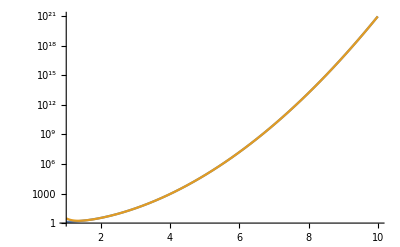

```mathematica
LogPlot[{Re[ParabolicCylinderD[-1/2,I √2 x]],ReICylSeries[x]},{x,1,10},PlotRange->All]
```

```mathematica
Simplify[Re[Normal[Series[ParabolicCylinderD[-1/2,√2 x],{x,∞,10}]]],Assumptions->x>0]
```

(ⅇ^(-x^2/2) (675675-221760 x^2+107520 x^4-98304 x^6+524288 x^8))/(524288 2^(1/4) x^(17/2))

```mathematica
Simplify[Im[Normal[Series[ParabolicCylinderD[-1/2,√2 x],{x,∞,10}]]],Assumptions->x>0]
```

0

```mathematica
CylSeries[x_]:=(ⅇ^(-x^2/2) (675675-221760 x^2+107520 x^4-98304 x^6+524288 x^8))/(524288 2^(1/4) x^(17/2))
```

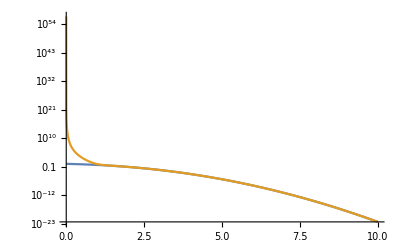

```mathematica
LogPlot[{ParabolicCylinderD[-1/2,√2 x],CylSeries[x]},{x,0,10},PlotRange->All]
```

```mathematica
"Yannis set up a clever way to obtain the string part of ImV by use of the Wronskian method taking into account the boundary conditions V'(0)=0 and V'(R_infty)=0";
```

```mathematica
FullImVWronskianAndMikko[mD_,T_,aFixed_,sFixed_,rmax_]:=Module[{Wron,xmax,xinfinityAt,RHSTable,RHSTableLow1,RHSTableLow2,RHSTableLow3,mu,SolutionTable,ImVTable,Minx,MinxStep,NSteps,InterpRHS,C1,Conv,x1fm},
Minx=1/50000;
MinxStep=1/200;
mu=(mD^2*sFixed/aFixed)^(1/4);
Conv=197/1000;
xmax=mu*rmax/Conv;
xinfinityAt=10000;
x1fm=mu*(1/2)/Conv;
Print["xmax:" ,xmax," xInfinity:", xinfinityAt];

Quiet[RHSTableLow1=Table[{x,-x^2 *NIntegrate[(2Sin[p *x])/((x)(p^2+mD^2/mu^2)),{p,0,∞},WorkingPrecision->32]},{x,Minx,10,MinxStep}];RHSTableLow2=Table[{x,-x^2 *NIntegrate[(2Sin[p *x])/((x)(p^2+mD^2/mu^2)),{p,0,∞},WorkingPrecision->32]},{x,10+MinxStep,200,10*MinxStep}];
RHSTableLow3=Table[{x,-x^2 *NIntegrate[(2Sin[p *x])/((x)(p^2+mD^2/mu^2)),{p,0,∞},WorkingPrecision->32]},{x,201,10500,500}];
RHSTable=Join[RHSTableLow1,RHSTableLow2,RHSTableLow3];
InterpRHS=Interpolation[RHSTable,InterpolationOrder->1];];
Print["InterpolationRHS: done"];

(*Print[Plot[InterpRHS[x],{x,0,12},PlotRange->All]];
Print[Plot[InterpRHS[x],{x,0,300},PlotRange->All]];*)

C1=   Re[ParabolicCylinderD[-1/2,ⅈ √2 Minx] NIntegrate[( InterpRHS[x])ParabolicCylinderD[-1/2,√2 x],{x,Minx,xinfinityAt},PrecisionGoal->1]];

NSteps=100;

SolutionTable=Join[Table[{xprime,C1-Re[ ParabolicCylinderD[-1/2,ⅈ √2 xprime]] NIntegrate[( InterpRHS[x])*ParabolicCylinderD[-1/2,√2 x],{x,xprime,xinfinityAt},PrecisionGoal->5,MaxRecursion->20]- ParabolicCylinderD[-1/2,√2 xprime]( NIntegrate[( InterpRHS[x])*Re[ParabolicCylinderD[-1/2,I √2 x]],{x,Minx,xprime},PrecisionGoal->5,MaxRecursion->20])},{xprime,Minx,x1fm,(x1fm-Minx)/(Floor[NSteps/3])}],Table[{xprime,C1-Re[ ParabolicCylinderD[-1/2,ⅈ √2 xprime]] NIntegrate[( InterpRHS[x])*ParabolicCylinderD[-1/2,√2 x],{x,xprime,xinfinityAt},PrecisionGoal->5,MaxRecursion->20]- ParabolicCylinderD[-1/2,√2 xprime]( NIntegrate[( InterpRHS[x])*Re[ParabolicCylinderD[-1/2,I √2 x]],{x,Minx,xprime},PrecisionGoal->5,MaxRecursion->20])},{xprime,x1fm+Minx,xmax,(xmax-(x1fm+Minx))/(NSteps-(Floor[NSteps/3]))}]];
Print[ListPlot[{Table[{SolutionTable[[k,1]]*Conv/mu,-(mD^2*sFixed*T)/mu^4*If[(SolutionTable[[k,2]]-SolutionTable[[1,2]])>0,0,(SolutionTable[[k,2]]-SolutionTable[[1,2]])]},{k,1,Length[SolutionTable]}],Table[{SolutionTable[[k,1]]*Conv/mu,aFixed*T*2*NIntegrate[(z/(z^2+1)^2)(1-Sin[(SolutionTable[[k,1]]*Conv/mu)/(197/1000)*mD* z]/((SolutionTable[[k,1]]*Conv/mu)/(197/1000)*mD* z)),{z,0,∞},PrecisionGoal->5,MaxRecursion->20]},{k,1,Length[SolutionTable]}]}]];
ImVTable=Table[{SolutionTable[[k,1]]*Conv/mu,-(mD^2*sFixed*T)/mu^4*If[(SolutionTable[[k,2]]-SolutionTable[[1,2]])
>0,0,(SolutionTable[[k,2]]-SolutionTable[[1,2]])]+aFixed*T*2*NIntegrate[(z/(z^2+1)^2)(1-Sin[(SolutionTable[[k,1]]*Conv/mu)/(197/1000)*mD* z]/((SolutionTable[[k,1]]*Conv/mu)/(197/1000)*mD* z)),{z,0,∞},PrecisionGoal->5,MaxRecursion->20]},{k,1,Length[SolutionTable]}];
(*Print[ListPlot[ImVTable,PlotRange->All]];*)
Return[ImVTable];
];
```

```mathematica
"Fix the values of alpha and sigma at the lowest temperature with a Cornell fit";
```

```mathematica
"b=6.900 T=41.05MeV Cornell Potential Fit1";
```

```mathematica
CurSet=1;
```

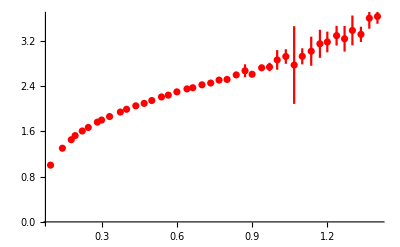

```mathematica
A[CurSet]=ErrorListPlot[PotReDataFull[CurSet],PlotStyle->{Red},PlotRange->All]
```

```mathematica
VaryFitLow={2,2,2,2,2,1,3,1,3}+1;
```

```mathematica
VaryFitHigh={24,28,26,30,22,24,24,26,22}-2;
```

```mathematica
Clear[PotFit];
```

```mathematica
1/PotReDataWeights[CurSet][[VaryFitLow[[0+1]];;VaryFitHigh[[0+1]] ]]
```

{2960.94,1847.8,1185.63,515.502,167.712,216.924,315.765,197.504,243.314,169.285,93.2215,156.99,123.515,61.8641,40.6411,41.2088,41.4078,48.7591,40.5467,34.6502}

```mathematica
Length[PotReData[CurSet][[VaryFitLow[[0+1]];;VaryFitHigh[[0+1]] ]]]
```

20

```mathematica
PotReData[CurSet][[VaryFitLow[[0+1]];;VaryFitHigh[[0+1]] ]]
```

{{0.178622,1.45157},{0.193976,1.52389},{0.222439,1.60556},{0.246457,1.66804},{0.282657,1.76151},{0.299479,1.79895},{0.331397,1.86068},{0.374401,1.94041},{0.399152,1.98932},{0.436007,2.05006},{0.469381,2.09346},{0.499678,2.14384},{0.538407,2.20699},{0.565571,2.23876},{0.599878,2.29672},{0.640182,2.34872},{0.66319,2.36937},{0.699858,2.42139},{0.734698,2.45272},{0.767959,2.50446}}

```mathematica
For[i=0,i<Length[VaryFitHigh],PotFit[CurSet][i]= NonlinearModelFit[PotReData[CurSet][[VaryFitLow[[i+1]];;VaryFitHigh[[i+1]] ]],{Re[CornellReV[x,ap,s,c]]},{{ap,0.3},{s,0.1},{c,3}},x,Method->LevenbergMarquardt,MaxIterations->1000,Weights->1/PotReDataWeights[CurSet][[VaryFitLow[[i+1]];;VaryFitHigh[[i+1]] ]] ];apTst[i]=ap/.PotFit[CurSet][i]["BestFitParameters"];sTst[i]=s/.PotFit[CurSet][i]["BestFitParameters"];
cTst[i]=c/.PotFit[CurSet][i]["BestFitParameters"];Print[apTst[i]," ",sTst[i]]; i++]
```

0.472847 0.217176

0.483676 0.211688

0.478425 0.214264

0.481873 0.212566

0.46905 0.219222

0.436651 0.229661

0.42536 0.230309

0.440718 0.226429

0.412214 0.236408

```mathematica
Clear[ApFitAvg];Clear[ApFitErr];Clear[SFitAvg];Clear[SFitErr];Clear[CFitAvg];Clear[CFitErr];Clear[FixedA];Clear[FixedAErr];Clear[FixedS];Clear[FixedSErr];Clear[FixedC];Clear[FixedCErr];
```

```mathematica
ApFitAvg[CurSet]=Mean[Table[apTst[k],{k,0,Length[VaryFitHigh]-1}]]
```

0.455646

```mathematica
ApFitErr[CurSet]=Sqrt[Variance[Table[apTst[k],{k,0,Length[VaryFitHigh]-1}]]]
```

0.0270538

```mathematica
SFitAvg[CurSet]=Mean[Table[sTst[k],{k,0,Length[VaryFitHigh]-1}]]
```

0.221969

```mathematica
SFitErr[CurSet]=Sqrt[Variance[Table[sTst[k],{k,0,Length[VaryFitHigh]-1}]]]
```

0.00895204

```mathematica
CFitAvg[CurSet]=Mean[Table[cTst[k],{k,0,Length[VaryFitHigh]-1}]]
```

1.76031

```mathematica
CFitErr[CurSet]=Sqrt[Variance[Table[cTst[k],{k,0,Length[VaryFitHigh]-1}]]]
```

0.0335099

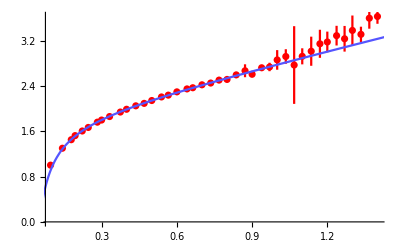

```mathematica
Show[A[CurSet],Plot[Re[CornellReV[r,ap,s,c]]/.PotFit[CurSet][1]["BestFitParameters"],{r,0.01,2},PlotRange->All,PlotStyle->Lighter[Blue]]]
```

```mathematica
FixedA[CurSet]=ApFitAvg[CurSet]
```

0.455646

```mathematica
FixedAErr[CurSet]=ApFitErr[CurSet]
```

0.0270538

```mathematica
FixedS[CurSet]=SFitAvg[CurSet]
```

0.221969

```mathematica
FixedSErr[CurSet]=SFitErr[CurSet];
```

```mathematica
Sqrt[FixedS[CurSet]]
```

0.471136

```mathematica
FixedC[CurSet]=CFitAvg[CurSet]
```

1.76031

```mathematica
FixedCErr[CurSet]=CFitErr[CurSet];
```

```mathematica
mDFitted[CurSet]=0.;
```

```mathematica
mDFittedErr[CurSet]=0.;
```

```mathematica
"b=7.480 T=71.54MeV Cornell Potential Fit1";
```

```mathematica
CurSet=2;
```

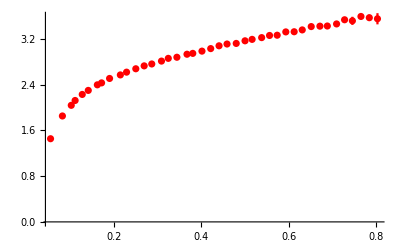

```mathematica
A[CurSet]=ErrorListPlot[PotReDataFull[CurSet],PlotStyle->{Red},PlotRange->All]
```

```mathematica
VaryFitLow={2,2,2,2,2,1,3,1,3}+4;
```

```mathematica
VaryFitHigh={24,28,26,30,22,24,24,26,22}+4;
```

```mathematica
Clear[PotFit];
```

```mathematica
For[i=0,i<Length[VaryFitHigh],PotFit[CurSet][i]= NonlinearModelFit[PotReData[CurSet][[VaryFitLow[[i+1]];;VaryFitHigh[[i+1]] ]],{Re[CornellReV[x,ap,s,c]]},{{ap,0.3},{s,0.1},{c,3}},x,Method->LevenbergMarquardt,MaxIterations->1000,Weights->1/PotReDataWeights[CurSet][[VaryFitLow[[i+1]];;VaryFitHigh[[i+1]] ]] ];apTst[i]=ap/.PotFit[CurSet][i]["BestFitParameters"];sTst[i]=s/.PotFit[CurSet][i]["BestFitParameters"];
cTst[i]=c/.PotFit[CurSet][i]["BestFitParameters"];Print[apTst[i]," ",sTst[i]]; i++]
```

0.384945 0.265541

0.394997 0.258985

0.388151 0.263346

0.390444 0.261815

0.38417 0.266108

0.375421 0.269331

0.387062 0.264764

0.378252 0.267029

0.386323 0.26525

```mathematica
ApFitAvg[CurSet]=Mean[Table[apTst[k],{k,0,Length[VaryFitHigh]-1}]]
```

0.38553

```mathematica
ApFitErr[CurSet]=Sqrt[Variance[Table[apTst[k],{k,0,Length[VaryFitHigh]-1}]]]
```

0.00592617

```mathematica
SFitAvg[CurSet]=Mean[Table[sTst[k],{k,0,Length[VaryFitHigh]-1}]]
```

0.264685

```mathematica
SFitErr[CurSet]=Sqrt[Variance[Table[sTst[k],{k,0,Length[VaryFitHigh]-1}]]]
```

0.00301425

```mathematica
CFitAvg[CurSet]=Mean[Table[cTst[k],{k,0,Length[VaryFitHigh]-1}]]
```

2.64796

```mathematica
CFitErr[CurSet]=Sqrt[Variance[Table[cTst[k],{k,0,Length[VaryFitHigh]-1}]]]
```

0.00884487

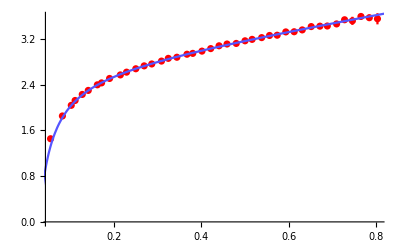

```mathematica
Show[A[CurSet],Plot[Re[CornellReV[r,ap,s,c]]/.PotFit[CurSet][1]["BestFitParameters"],{r,0.01,2},PlotRange->All,PlotStyle->Lighter[Blue]]]
```

```mathematica
FixedA[CurSet]=ApFitAvg[CurSet]
```

0.38553

```mathematica
FixedAErr[CurSet]=ApFitErr[CurSet]
```

0.00592617

```mathematica
FixedS[CurSet]=SFitAvg[CurSet]
```

0.264685

```mathematica
FixedSErr[CurSet]=SFitErr[CurSet]
```

0.00301425

```mathematica
Sqrt[FixedS[CurSet]]
```

0.514476

```mathematica
FixedC[CurSet]=CFitAvg[CurSet]
```

2.64796

```mathematica
FixedCErr[CurSet]=CFitErr[CurSet];
```

```mathematica
mDFitted[CurSet]=0.;
```

```mathematica
mDFittedErr[CurSet]=0.;
```

```mathematica
NewPotReDataFull=Table[{PotReDataFull[2][[k,1]],PotReDataFull[2][[k,2]]-1,PotReDataFull[2][[k,3]]},{k,1,Length[PotReDataFull[2]]}]
```

{{0.0550702,0.455857,0.00046998},{0.0822327,0.854048,0.000766737},{0.102498,1.04039,0.00172637},{0.111308,1.12513,0.0010727},{0.127641,1.23105,0.00349064},{0.141423,1.30142,0.00662794},{0.162196,1.39922,0.00635471},{0.171849,1.43314,0.006347},{0.190164,1.51057,0.00832274},{0.214841,1.57259,0.00987728},{0.229044,1.62098,0.00688682},{0.250192,1.68033,0.00998829},{0.269343,1.73093,0.00640482},{0.286728,1.76422,0.0121793},{0.308952,1.81468,0.0136992},{0.324539,1.86241,0.00555948},{0.344225,1.88189,0.0130363},{0.367353,1.93464,0.0100476},{0.380555,1.94959,0.0172723},{0.401596,1.98901,0.0122884},{0.421588,2.0332,0.00938452},{0.440674,2.08223,0.015494},{0.458967,2.11344,0.0249399},{0.479999,2.12377,0.0199609},{0.500148,2.16965,0.0168181},{0.516338,2.19472,0.0188426},{0.538187,2.22551,0.0216129},{0.556231,2.26301,0.0223027},{0.573709,2.26751,0.0259667},{0.593449,2.3254,0.0299835},{0.612554,2.32827,0.0324685},{0.63108,2.36042,0.0293922},{0.651608,2.41877,0.018246},{0.671509,2.42588,0.0335708},{0.688451,2.42872,0.0417955},{0.709639,2.46491,0.0345045},{0.727955,2.53795,0.0361795},{0.745822,2.51941,0.0709328},{0.765423,2.5958,0.0179597},{0.784535,2.57394,0.0526286},{0.803192,2.55524,0.0978076}}

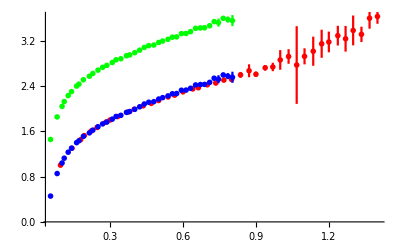

```mathematica
ErrorListPlot[{PotReDataFull[1],PotReDataFull[2],NewPotReDataFull},PlotStyle->{{Red,PointSize[0.01]},{Green,PointSize[0.01]},{Blue,PointSize[0.01]}},PlotRange->All]
```

```mathematica
"Interpolate between the low T sets both in the values of the fitted parameters and their relative errors.";
```

```mathematica
((FixedA[2]-FixedA[1])/(7.480-6.90))
```

-0.120891

```mathematica
AlphaIntFit=FindFit[{{6.90,FixedA[1]},{7.48,FixedA[2]}},A1*b+A2,{A1,A2},b]
```

{A1→-0.120891,A2→1.28979}

```mathematica
AlphaRelErrIntFit=FindFit[{{6.90,FixedAErr[1]/FixedA[1]},{7.48,FixedAErr[2]/FixedA[2]}},A1*b+A2,{A1,A2},b]
```

{A1→-0.0758673,A2→0.582859}

```mathematica
AlphaInt[b_]:=(A1*b+A2)/.AlphaIntFit
```

```mathematica
AlphaRelErrInt[b_]:=(A1*b+A2)/.AlphaRelErrIntFit
```

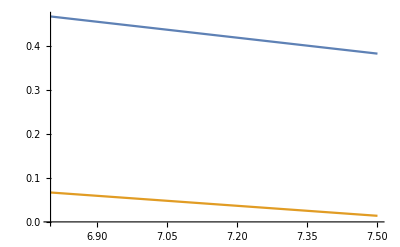

```mathematica
Plot[{AlphaInt[b],AlphaRelErrInt[b]},{b,6.8,7.5}]
```

```mathematica
SigmaIntFit=FindFit[{{6.90,FixedS[1]},{7.48,FixedS[2]}},S1*b+S2,{S1,S2},b]
```

{S1→0.0736487,S2→-0.286207}

```mathematica
SigmaRelErrIntFit=FindFit[{{6.90,FixedSErr[1]/FixedS[1]},{7.48,FixedSErr[2]/FixedS[2]}},S1*b+S2,{S1,S2},b]
```

{S1→-0.0499001,S2→0.384641}

```mathematica
SigmaInt[b_]:=(S1*b+S2)/.SigmaIntFit
```

```mathematica
SigmaRelErrInt[b_]:=(S1*b+S2)/.SigmaRelErrIntFit
```

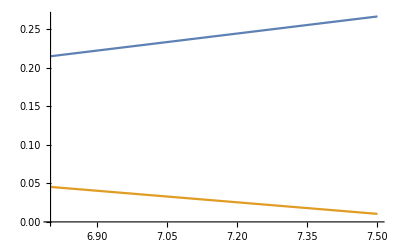

```mathematica
Plot[{SigmaInt[b],SigmaRelErrInt[b]},{b,6.8,7.5}]
```

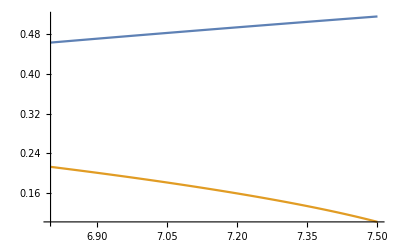

```mathematica
Plot[{Sqrt[SigmaInt[b]],Sqrt[SigmaRelErrInt[b]]},{b,6.8,7.5}]
```

```mathematica
ShiftCIntFit=FindFit[{{6.90,FixedC[1]},{7.48,FixedC[2]}},C1*b+C2,{C1,C2},b]
```

{C1→1.53044,C2→-8.79976}

```mathematica
ShiftCRelErrIntFit=FindFit[{{6.90,FixedCErr[1]/FixedC[1]},{7.48,FixedCErr[2]/FixedC[2]}},C1*b+C2,{C1,C2},b]
```

{C1→-0.0270624,C2→0.205767}

```mathematica
ShiftCInt[b_]:=(C1*b+C2)/.ShiftCIntFit
```

```mathematica
ShiftCRelErrInt[b_]:=(C1*b+C2)/.ShiftCRelErrIntFit
```

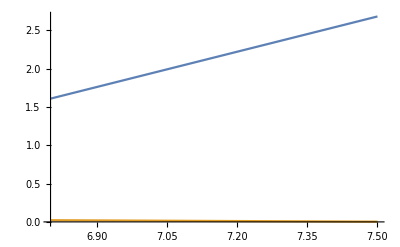

```mathematica
Plot[{ShiftCInt[b],ShiftCRelErrInt[b]},{b,6.8,7.5}]
```

```mathematica
"Now carry out the fits at the different finite temperatures";
```

```mathematica
VariationFactor=0.45;
```

```mathematica
"beta=7.480 T=286.1MeV Real Part";
```

```mathematica
CurSet=9;
```

```mathematica
Temp[CurSet]=0.2861;
```

```mathematica
CurBeta=7.48;
```

```mathematica
VaryAandCandS={  {AlphaInt[CurBeta],SigmaInt[CurBeta],ShiftCInt[CurBeta]},{AlphaInt[CurBeta],SigmaInt[CurBeta],ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta],SigmaInt[CurBeta],ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},
{AlphaInt[CurBeta],SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta],SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta],SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta],SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta],SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta],SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor}};
```

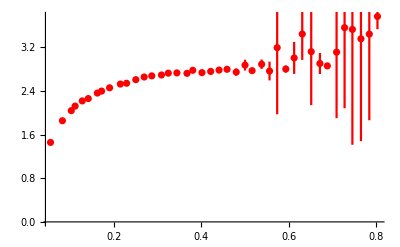

```mathematica
A[CurSet]=ErrorListPlot[PotReDataFull[CurSet],PlotStyle->{Red},PlotRange->All]
```

```mathematica
VaryFitLow={2,2,2,2,2,1,3,1,3};
VaryFitHigh={32,28,26,24,20,22,22,30,30}-2;
```

```mathematica
For[i=0,i<Length[VaryFitHigh],i++,
(*Here we vary the fitting range as specified by VaryFitLow and VaryFitHigh*)
For[j=0,j<27,j++,
(*Here we vary the for each fitting range the parameters determined at T=0*)

PotFit[CurSet][i*27+j]= NonlinearModelFit[PotReData[CurSet][[VaryFitLow[[i+1]];;VaryFitHigh[[i+1]] ]],{Re[DebyeHueckelReV[x,VaryAandCandS[[j+1]][[1]],VaryAandCandS[[j+1]][[2]],mD,VaryAandCandS[[j+1]][[3]]]]},{{mD,0.1}},x,Method->LevenbergMarquardt,MaxIterations->1000];mDTst[i*27+j]=mD/.PotFit[CurSet][i*27+j]["BestFitParameters"];
(*Print[mDTst[i*27+j]," "]*); ];]
```

```mathematica
mDFitted[CurSet]=Mean[Table[mDTst[k], {k,0,27*Length[VaryFitHigh]-1}]]
```

0.655407

```mathematica
mDFittedErr[CurSet]=StandardDeviation[Table[mDTst[k], {k,0,27*Length[VaryFitHigh]-1}]]
```

0.0393411

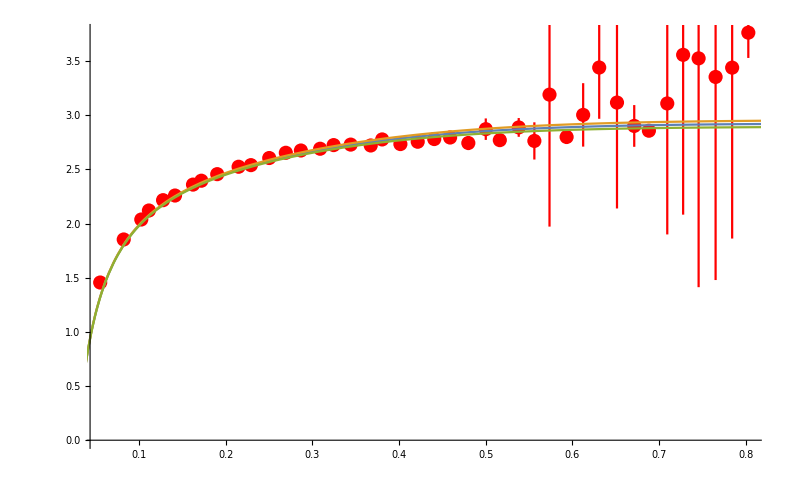

```mathematica
Show[A[CurSet],Plot[{Re[DebyeHueckelReV[r,AlphaInt[CurBeta],SigmaInt[CurBeta],mDFitted[CurSet],ShiftCInt[CurBeta]]],Re[DebyeHueckelReV[r,AlphaInt[CurBeta],SigmaInt[CurBeta],mDFitted[CurSet]-mDFittedErr[CurSet],ShiftCInt[CurBeta]]],Re[DebyeHueckelReV[r,AlphaInt[CurBeta],SigmaInt[CurBeta],mDFitted[CurSet]+mDFittedErr[CurSet],ShiftCInt[CurBeta]]]},{r,0.01,2},PlotRange->All]]
```

```mathematica
"Imaginary Part";
```

```mathematica
AI[CurSet]=ErrorListPlot[PotImDataFull[CurSet],PlotStyle->{Red},PlotRange->{{0,2.5},{0,1.2}}];
```

```mathematica
AIClose[CurSet]=ErrorListPlot[PotImDataFull[CurSet],PlotStyle->{Red},PlotRange->{{0,0.3},{0,0.2}}];
```

```mathematica
If[FileExistsQ[ToString@StringForm["./ResultsDynamical/ImVWronskian1_``.dat",CurSet]],ImVWronskian1=Import[ToString@StringForm["./ResultsDynamical/ImVWronskian1_``.dat",CurSet]],ImVWronskian1=FullImVWronskianAndMikko[mDFitted[CurSet],Temp[CurSet],AlphaInt[CurBeta],SigmaInt[CurBeta],10.];Export[ToString@StringForm["./ResultsDynamical/ImVWronskian1_``.dat",CurSet],ImVWronskian1,InterpolationOrder->2]];
```

```mathematica
InterpImVFull1[CurSet]=Interpolation[ImVWronskian1,InterpolationOrder->2];
```

```mathematica
If[FileExistsQ[ToString@StringForm["./ResultsDynamical/ImVWronskian2_``.dat",CurSet]],ImVWronskian2=Import[ToString@StringForm["./ResultsDynamical/ImVWronskian2_``.dat",CurSet]],ImVWronskian2=FullImVWronskianAndMikko[mDFitted[CurSet]+mDFittedErr[CurSet],Temp[CurSet],AlphaInt[CurBeta],SigmaInt[CurBeta],10.];Export[ToString@StringForm["./ResultsDynamical/ImVWronskian2_``.dat",CurSet],ImVWronskian2,InterpolationOrder->2]];
```

```mathematica
InterpImVFull2[CurSet]=Interpolation[ImVWronskian2,InterpolationOrder->2];
```

```mathematica
If[FileExistsQ[ToString@StringForm["./ResultsDynamical/ImVWronskian3_``.dat",CurSet]],ImVWronskian3=Import[ToString@StringForm["./ResultsDynamical/ImVWronskian3_``.dat",CurSet]],ImVWronskian3=FullImVWronskianAndMikko[mDFitted[CurSet]-mDFittedErr[CurSet],Temp[CurSet],AlphaInt[CurBeta],SigmaInt[CurBeta],10.];Export[ToString@StringForm["./ResultsDynamical/ImVWronskian3_``.dat",CurSet],ImVWronskian3,InterpolationOrder->2]];
```

```mathematica
InterpImVFull3[CurSet]=Interpolation[ImVWronskian3,InterpolationOrder->2];
```

```mathematica
"Plotting the fit for ImV";
```

```mathematica
AIDH[CurSet]=Plot[{InterpImVFull1[CurSet][r],InterpImVFull2[CurSet][r],InterpImVFull3[CurSet][r]},{r,0.01,2.5}];
```

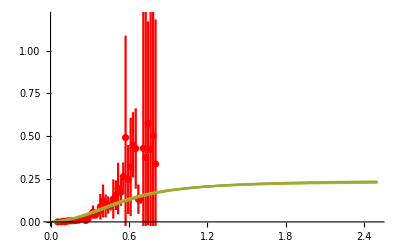

```mathematica
Show[AI[CurSet],AIDH[CurSet]]
```

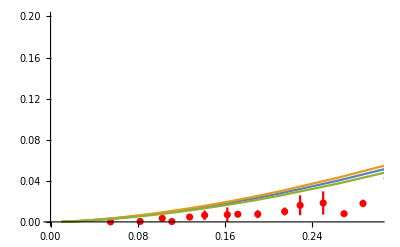

```mathematica
Show[AIClose[CurSet],AIDH[CurSet]]
```

```mathematica
"beta=7.300 T=242.5MeV Real Part";
```

```mathematica
CurSet=8;
```

```mathematica
Temp[CurSet]=0.2425;
```

```mathematica
CurBeta=7.3;
```

```mathematica
VaryAandCandS={  {AlphaInt[CurBeta],SigmaInt[CurBeta],ShiftCInt[CurBeta]},{AlphaInt[CurBeta],SigmaInt[CurBeta],ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta],SigmaInt[CurBeta],ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},
{AlphaInt[CurBeta],SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta],SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta],SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta],SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta],SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta],SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor}};
```

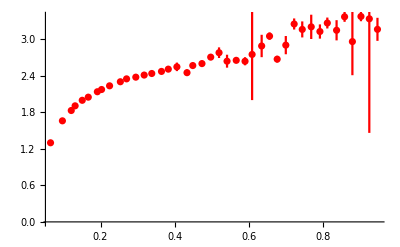

```mathematica
A[CurSet]=ErrorListPlot[PotReDataFull[CurSet],PlotStyle->{Red},PlotRange->All]
```

```mathematica
VaryFitLow={2,2,2,2,2,1,3,1,3};
VaryFitHigh={32,28,26,24,20,22,22,30,30}-2;
```

```mathematica
For[i=0,i<Length[VaryFitHigh],i++,
(*Here we vary the fitting range as specified by VaryFitLow and VaryFitHigh*)
For[j=0,j<27,j++,
(*Here we vary the for each fitting range the parameters determined at T=0*)

PotFit[CurSet][i*27+j]= NonlinearModelFit[PotReData[CurSet][[VaryFitLow[[i+1]];;VaryFitHigh[[i+1]] ]],{Re[DebyeHueckelReV[x,VaryAandCandS[[j+1]][[1]],VaryAandCandS[[j+1]][[2]],mD,VaryAandCandS[[j+1]][[3]]]]},{{mD,0.1}},x,Method->LevenbergMarquardt,MaxIterations->1000];mDTst[i*27+j]=mD/.PotFit[CurSet][i*27+j]["BestFitParameters"];
(*Print[mDTst[i*27+j]," "]*); ];]
```

```mathematica
mDFitted[CurSet]=Mean[Table[mDTst[k], {k,0,27*Length[VaryFitHigh]-1}]]
```

0.497157

```mathematica
mDFittedErr[CurSet]=StandardDeviation[Table[mDTst[k], {k,0,27*Length[VaryFitHigh]-1}]]
```

0.0653966

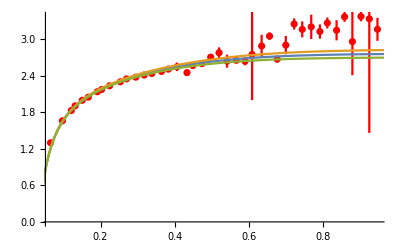

```mathematica
Show[A[CurSet],Plot[{Re[DebyeHueckelReV[r,AlphaInt[CurBeta],SigmaInt[CurBeta],mDFitted[CurSet],ShiftCInt[CurBeta]]],Re[DebyeHueckelReV[r,AlphaInt[CurBeta],SigmaInt[CurBeta],mDFitted[CurSet]-mDFittedErr[CurSet],ShiftCInt[CurBeta]]],Re[DebyeHueckelReV[r,AlphaInt[CurBeta],SigmaInt[CurBeta],mDFitted[CurSet]+mDFittedErr[CurSet],ShiftCInt[CurBeta]]]},{r,0.01,2},PlotRange->All]]
```

```mathematica
"Imaginary Part";
```

```mathematica
AI[CurSet]=ErrorListPlot[PotImDataFull[CurSet],PlotStyle->{Red},PlotRange->{{0,2.5},{0,1.2}}];
```

```mathematica
AIClose[CurSet]=ErrorListPlot[PotImDataFull[CurSet],PlotStyle->{Red},PlotRange->{{0,0.3},{0,0.2}}];
```

```mathematica
If[FileExistsQ[ToString@StringForm["./ResultsDynamical/ImVWronskian1_``.dat",CurSet]],ImVWronskian1=Import[ToString@StringForm["./ResultsDynamical/ImVWronskian1_``.dat",CurSet]],ImVWronskian1=FullImVWronskianAndMikko[mDFitted[CurSet],Temp[CurSet],AlphaInt[CurBeta],SigmaInt[CurBeta],10.];Export[ToString@StringForm["./ResultsDynamical/ImVWronskian1_``.dat",CurSet],ImVWronskian1,InterpolationOrder->2]];
```

```mathematica
InterpImVFull1[CurSet]=Interpolation[ImVWronskian1,InterpolationOrder->2];
```

```mathematica
If[FileExistsQ[ToString@StringForm["./ResultsDynamical/ImVWronskian2_``.dat",CurSet]],ImVWronskian2=Import[ToString@StringForm["./ResultsDynamical/ImVWronskian2_``.dat",CurSet]],ImVWronskian2=FullImVWronskianAndMikko[mDFitted[CurSet]+mDFittedErr[CurSet],Temp[CurSet],AlphaInt[CurBeta],SigmaInt[CurBeta],10.];Export[ToString@StringForm["./ResultsDynamical/ImVWronskian2_``.dat",CurSet],ImVWronskian2,InterpolationOrder->2]];
```

```mathematica
InterpImVFull2[CurSet]=Interpolation[ImVWronskian2,InterpolationOrder->2];
```

```mathematica
If[FileExistsQ[ToString@StringForm["./ResultsDynamical/ImVWronskian3_``.dat",CurSet]],ImVWronskian3=Import[ToString@StringForm["./ResultsDynamical/ImVWronskian3_``.dat",CurSet]],ImVWronskian3=FullImVWronskianAndMikko[mDFitted[CurSet]-mDFittedErr[CurSet],Temp[CurSet],AlphaInt[CurBeta],SigmaInt[CurBeta],10.];Export[ToString@StringForm["./ResultsDynamical/ImVWronskian3_``.dat",CurSet],ImVWronskian3,InterpolationOrder->2]];
```

```mathematica
InterpImVFull3[CurSet]=Interpolation[ImVWronskian3,InterpolationOrder->2];
```

```mathematica
"Plotting the fit for ImV";
```

```mathematica
AIDH[CurSet]=Plot[{InterpImVFull1[CurSet][r],InterpImVFull2[CurSet][r],InterpImVFull3[CurSet][r]},{r,0.01,2.5}];
```

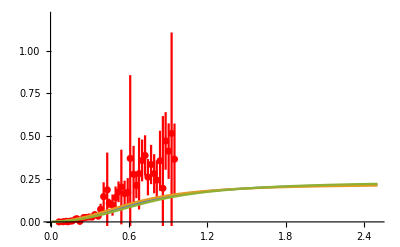

```mathematica
Show[AI[CurSet],AIDH[CurSet]]
```

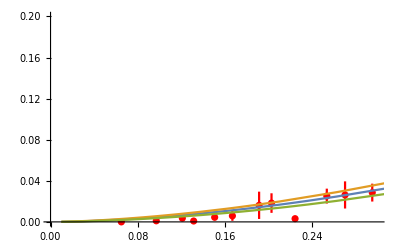

```mathematica
Show[AIClose[CurSet],AIDH[CurSet]]
```

```mathematica
"beta=7.250 T=231.7MeV Real Part";
```

```mathematica
CurSet=7;
```

```mathematica
Temp[CurSet]=0.2317;
```

```mathematica
CurBeta=7.25;
```

```mathematica
VaryAandCandS={  {AlphaInt[CurBeta],SigmaInt[CurBeta],ShiftCInt[CurBeta]},{AlphaInt[CurBeta],SigmaInt[CurBeta],ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta],SigmaInt[CurBeta],ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},
{AlphaInt[CurBeta],SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta],SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta],SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta],SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta],SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta],SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor}};
```

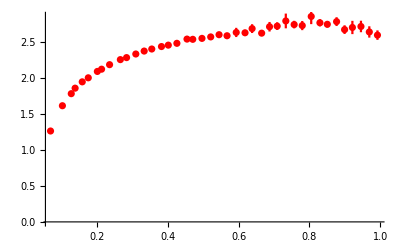

```mathematica
A[CurSet]=ErrorListPlot[PotReDataFull[CurSet],PlotStyle->{Red},PlotRange->All]
```

```mathematica
VaryFitLow={2,2,2,2,2,1,3,1,3};
VaryFitHigh={32,28,26,24,20,22,22,30,30}-2;
```

```mathematica
For[i=0,i<Length[VaryFitHigh],i++,
(*Here we vary the fitting range as specified by VaryFitLow and VaryFitHigh*)
For[j=0,j<27,j++,
(*Here we vary the for each fitting range the parameters determined at T=0*)

PotFit[CurSet][i*27+j]= NonlinearModelFit[PotReData[CurSet][[VaryFitLow[[i+1]];;VaryFitHigh[[i+1]] ]],{Re[DebyeHueckelReV[x,VaryAandCandS[[j+1]][[1]],VaryAandCandS[[j+1]][[2]],mD,VaryAandCandS[[j+1]][[3]]]]},{{mD,0.1}},x,Method->LevenbergMarquardt,MaxIterations->1000];mDTst[i*27+j]=mD/.PotFit[CurSet][i*27+j]["BestFitParameters"];
(*Print[mDTst[i*27+j]," "]*); ];]
```

```mathematica
mDFitted[CurSet]=Mean[Table[mDTst[k], {k,0,27*Length[VaryFitHigh]-1}]]
```

0.479708

```mathematica
mDFittedErr[CurSet]=StandardDeviation[Table[mDTst[k], {k,0,27*Length[VaryFitHigh]-1}]]
```

0.026445

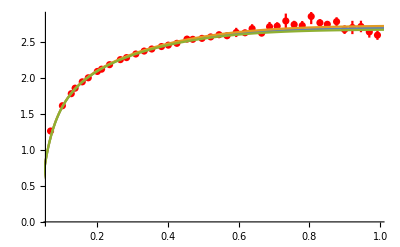

```mathematica
Show[A[CurSet],Plot[{Re[DebyeHueckelReV[r,AlphaInt[CurBeta],SigmaInt[CurBeta],mDFitted[CurSet],ShiftCInt[CurBeta]]],Re[DebyeHueckelReV[r,AlphaInt[CurBeta],SigmaInt[CurBeta],mDFitted[CurSet]-mDFittedErr[CurSet],ShiftCInt[CurBeta]]],Re[DebyeHueckelReV[r,AlphaInt[CurBeta],SigmaInt[CurBeta],mDFitted[CurSet]+mDFittedErr[CurSet],ShiftCInt[CurBeta]]]},{r,0.01,2},PlotRange->All]]
```

```mathematica
"Imaginary Part";
```

```mathematica
AI[CurSet]=ErrorListPlot[PotImDataFull[CurSet],PlotStyle->{Red},PlotRange->{{0,2.5},{0,1.2}}];
```

```mathematica
AIClose[CurSet]=ErrorListPlot[PotImDataFull[CurSet],PlotStyle->{Red},PlotRange->{{0,0.3},{0,0.2}}];
```

```mathematica
If[FileExistsQ[ToString@StringForm["./ResultsDynamical/ImVWronskian1_``.dat",CurSet]],ImVWronskian1=Import[ToString@StringForm["./ResultsDynamical/ImVWronskian1_``.dat",CurSet]],ImVWronskian1=FullImVWronskianAndMikko[mDFitted[CurSet],Temp[CurSet],AlphaInt[CurBeta],SigmaInt[CurBeta],10.];Export[ToString@StringForm["./ResultsDynamical/ImVWronskian1_``.dat",CurSet],ImVWronskian1,InterpolationOrder->2]];
```

```mathematica
InterpImVFull1[CurSet]=Interpolation[ImVWronskian1,InterpolationOrder->2];
```

```mathematica
If[FileExistsQ[ToString@StringForm["./ResultsDynamical/ImVWronskian2_``.dat",CurSet]],ImVWronskian2=Import[ToString@StringForm["./ResultsDynamical/ImVWronskian2_``.dat",CurSet]],ImVWronskian2=FullImVWronskianAndMikko[mDFitted[CurSet]+mDFittedErr[CurSet],Temp[CurSet],AlphaInt[CurBeta],SigmaInt[CurBeta],10.];Export[ToString@StringForm["./ResultsDynamical/ImVWronskian2_``.dat",CurSet],ImVWronskian2,InterpolationOrder->2]];
```

```mathematica
InterpImVFull2[CurSet]=Interpolation[ImVWronskian2,InterpolationOrder->2];
```

```mathematica
If[FileExistsQ[ToString@StringForm["./ResultsDynamical/ImVWronskian3_``.dat",CurSet]],ImVWronskian3=Import[ToString@StringForm["./ResultsDynamical/ImVWronskian3_``.dat",CurSet]],ImVWronskian3=FullImVWronskianAndMikko[mDFitted[CurSet]-mDFittedErr[CurSet],Temp[CurSet],AlphaInt[CurBeta],SigmaInt[CurBeta],10.];Export[ToString@StringForm["./ResultsDynamical/ImVWronskian3_``.dat",CurSet],ImVWronskian3,InterpolationOrder->2]];
```

```mathematica
InterpImVFull3[CurSet]=Interpolation[ImVWronskian3,InterpolationOrder->2];
```

```mathematica
"Plotting the fit for ImV";
```

```mathematica
AIDH[CurSet]=Plot[{InterpImVFull1[CurSet][r],InterpImVFull2[CurSet][r],InterpImVFull3[CurSet][r]},{r,0.01,2.5}];
```

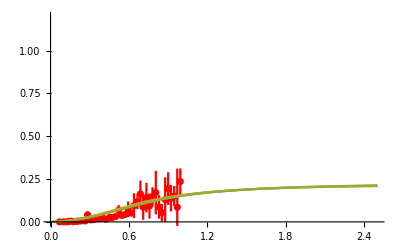

```mathematica
Show[AI[CurSet],AIDH[CurSet]]
```

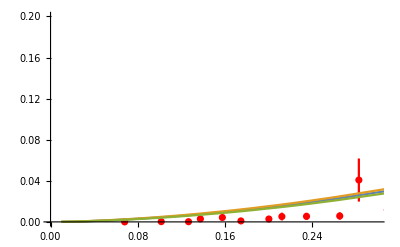

```mathematica
Show[AIClose[CurSet],AIDH[CurSet]]
```

```mathematica
"beta=7.125 T=205.4MeV Real Part";
```

```mathematica
CurSet=6;
```

```mathematica
Temp[CurSet]=0.2054;
```

```mathematica
CurBeta=7.125;
```

```mathematica
VaryAandCandS={  {AlphaInt[CurBeta],SigmaInt[CurBeta],ShiftCInt[CurBeta]},{AlphaInt[CurBeta],SigmaInt[CurBeta],ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta],SigmaInt[CurBeta],ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},
{AlphaInt[CurBeta],SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta],SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta],SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta],SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta],SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta],SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor}};
```

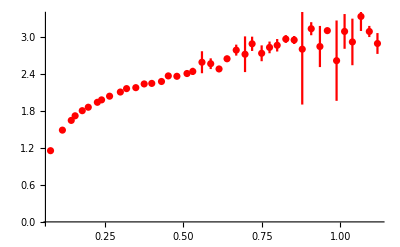

```mathematica
A[CurSet]=ErrorListPlot[PotReDataFull[CurSet],PlotStyle->{Red},PlotRange->All]
```

```mathematica
VaryFitLow={2,2,2,2,2,1,3,1,3};
VaryFitHigh={32,28,26,24,20,22,22,30,30}-2;
```

```mathematica
For[i=0,i<Length[VaryFitHigh],i++,
(*Here we vary the fitting range as specified by VaryFitLow and VaryFitHigh*)
For[j=0,j<27,j++,
(*Here we vary the for each fitting range the parameters determined at T=0*)

PotFit[CurSet][i*27+j]= NonlinearModelFit[PotReData[CurSet][[VaryFitLow[[i+1]];;VaryFitHigh[[i+1]] ]],{Re[DebyeHueckelReV[x,VaryAandCandS[[j+1]][[1]],VaryAandCandS[[j+1]][[2]],mD,VaryAandCandS[[j+1]][[3]]]]},{{mD,0.1}},x,Method->LevenbergMarquardt,MaxIterations->1000];mDTst[i*27+j]=mD/.PotFit[CurSet][i*27+j]["BestFitParameters"];
(*Print[mDTst[i*27+j]," "]*); ];]
```

```mathematica
mDFitted[CurSet]=Mean[Table[mDTst[k], {k,0,27*Length[VaryFitHigh]-1}]]
```

0.262888

```mathematica
mDFittedErr[CurSet]=StandardDeviation[Table[mDTst[k], {k,0,27*Length[VaryFitHigh]-1}]]
```

0.0999302

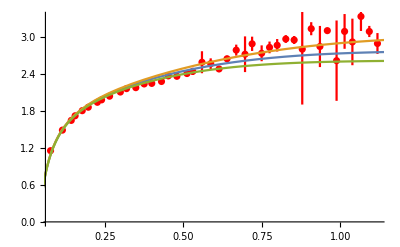

```mathematica
Show[A[CurSet],Plot[{Re[DebyeHueckelReV[r,AlphaInt[CurBeta],SigmaInt[CurBeta],mDFitted[CurSet],ShiftCInt[CurBeta]]],Re[DebyeHueckelReV[r,AlphaInt[CurBeta],SigmaInt[CurBeta],mDFitted[CurSet]-mDFittedErr[CurSet],ShiftCInt[CurBeta]]],Re[DebyeHueckelReV[r,AlphaInt[CurBeta],SigmaInt[CurBeta],mDFitted[CurSet]+mDFittedErr[CurSet],ShiftCInt[CurBeta]]]},{r,0.01,2},PlotRange->All]]
```

```mathematica
"Imaginary Part";
```

```mathematica
AI[CurSet]=ErrorListPlot[PotImDataFull[CurSet],PlotStyle->{Red},PlotRange->{{0,2.5},{0,1.2}}];
```

```mathematica
AIClose[CurSet]=ErrorListPlot[PotImDataFull[CurSet],PlotStyle->{Red},PlotRange->{{0,0.3},{0,0.2}}];
```

```mathematica
If[FileExistsQ[ToString@StringForm["./ResultsDynamical/ImVWronskian1_``.dat",CurSet]],ImVWronskian1=Import[ToString@StringForm["./ResultsDynamical/ImVWronskian1_``.dat",CurSet]],ImVWronskian1=FullImVWronskianAndMikko[mDFitted[CurSet],Temp[CurSet],AlphaInt[CurBeta],SigmaInt[CurBeta],10.];Export[ToString@StringForm["./ResultsDynamical/ImVWronskian1_``.dat",CurSet],ImVWronskian1,InterpolationOrder->2]];
```

```mathematica
InterpImVFull1[CurSet]=Interpolation[ImVWronskian1,InterpolationOrder->2];
```

```mathematica
If[FileExistsQ[ToString@StringForm["./ResultsDynamical/ImVWronskian2_``.dat",CurSet]],ImVWronskian2=Import[ToString@StringForm["./ResultsDynamical/ImVWronskian2_``.dat",CurSet]],ImVWronskian2=FullImVWronskianAndMikko[mDFitted[CurSet]+mDFittedErr[CurSet],Temp[CurSet],AlphaInt[CurBeta],SigmaInt[CurBeta],10.];Export[ToString@StringForm["./ResultsDynamical/ImVWronskian2_``.dat",CurSet],ImVWronskian2,InterpolationOrder->2]];
```

```mathematica
InterpImVFull2[CurSet]=Interpolation[ImVWronskian2,InterpolationOrder->2];
```

```mathematica
If[FileExistsQ[ToString@StringForm["./ResultsDynamical/ImVWronskian3_``.dat",CurSet]],ImVWronskian3=Import[ToString@StringForm["./ResultsDynamical/ImVWronskian3_``.dat",CurSet]],ImVWronskian3=FullImVWronskianAndMikko[mDFitted[CurSet]-mDFittedErr[CurSet],Temp[CurSet],AlphaInt[CurBeta],SigmaInt[CurBeta],10.];Export[ToString@StringForm["./ResultsDynamical/ImVWronskian3_``.dat",CurSet],ImVWronskian3,InterpolationOrder->2]];
```

```mathematica
InterpImVFull3[CurSet]=Interpolation[ImVWronskian3,InterpolationOrder->2];
```

```mathematica
"Plotting the fit for ImV";
```

```mathematica
AIDH[CurSet]=Plot[{InterpImVFull1[CurSet][r],InterpImVFull2[CurSet][r],InterpImVFull3[CurSet][r]},{r,0.01,2.5}];
```

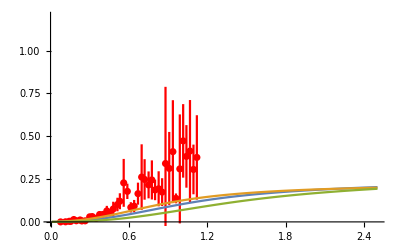

```mathematica
Show[AI[CurSet],AIDH[CurSet]]
```

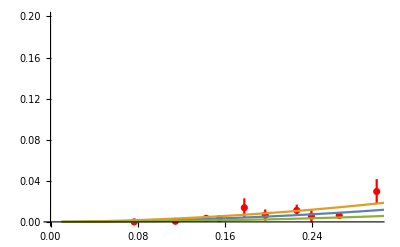

```mathematica
Show[AIClose[CurSet],AIDH[CurSet]]
```

```mathematica
"beta=7.000 T=181.8MeV Real Part";
```

```mathematica
CurSet=5;
```

```mathematica
Temp[CurSet]=0.1818;
```

```mathematica
CurBeta=7.000;
```

```mathematica
VaryAandCandS={  {AlphaInt[CurBeta],SigmaInt[CurBeta],ShiftCInt[CurBeta]},{AlphaInt[CurBeta],SigmaInt[CurBeta],ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta],SigmaInt[CurBeta],ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},
{AlphaInt[CurBeta],SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta],SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta],SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta],SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta],SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta],SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor}};
```

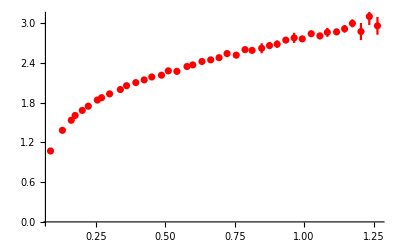

```mathematica
A[CurSet]=ErrorListPlot[PotReDataFull[CurSet],PlotStyle->{Red},PlotRange->All]
```

```mathematica
VaryFitLow={2,2,2,2,2,1,3,1,3};
VaryFitHigh={32,28,26,24,20,22,22,30,30}-2;
```

```mathematica
For[i=0,i<Length[VaryFitHigh],i++,
(*Here we vary the fitting range as specified by VaryFitLow and VaryFitHigh*)
For[j=0,j<27,j++,
(*Here we vary the for each fitting range the parameters determined at T=0*)

PotFit[CurSet][i*27+j]= NonlinearModelFit[PotReData[CurSet][[VaryFitLow[[i+1]];;VaryFitHigh[[i+1]] ]],{Re[DebyeHueckelReV[x,VaryAandCandS[[j+1]][[1]],VaryAandCandS[[j+1]][[2]],mD,VaryAandCandS[[j+1]][[3]]]]},{{mD,0.1}},x,Method->LevenbergMarquardt,MaxIterations->1000];mDTst[i*27+j]=mD/.PotFit[CurSet][i*27+j]["BestFitParameters"];
(*Print[mDTst[i*27+j]," "]*); ];]
```

```mathematica
mDFitted[CurSet]=Mean[Table[mDTst[k], {k,0,27*Length[VaryFitHigh]-1}]]
```

0.18708

```mathematica
mDFittedErr[CurSet]=StandardDeviation[Table[mDTst[k], {k,0,27*Length[VaryFitHigh]-1}]]
```

0.0402694

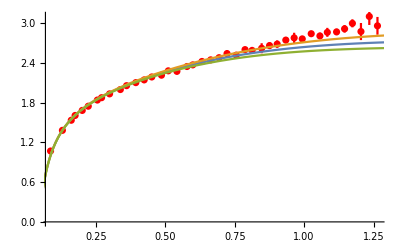

```mathematica
Show[A[CurSet],Plot[{Re[DebyeHueckelReV[r,AlphaInt[CurBeta],SigmaInt[CurBeta],mDFitted[CurSet],ShiftCInt[CurBeta]]],Re[DebyeHueckelReV[r,AlphaInt[CurBeta],SigmaInt[CurBeta],mDFitted[CurSet]-mDFittedErr[CurSet],ShiftCInt[CurBeta]]],Re[DebyeHueckelReV[r,AlphaInt[CurBeta],SigmaInt[CurBeta],mDFitted[CurSet]+mDFittedErr[CurSet],ShiftCInt[CurBeta]]]},{r,0.01,2},PlotRange->All]]
```

```mathematica
"Imaginary Part";
```

```mathematica
AI[CurSet]=ErrorListPlot[PotImDataFull[CurSet],PlotStyle->{Red},PlotRange->{{0,2.5},{0,1.2}}];
```

```mathematica
AIClose[CurSet]=ErrorListPlot[PotImDataFull[CurSet],PlotStyle->{Red},PlotRange->{{0,0.3},{0,0.2}}];
```

```mathematica
If[FileExistsQ[ToString@StringForm["./ResultsDynamical/ImVWronskian1_``.dat",CurSet]],ImVWronskian1=Import[ToString@StringForm["./ResultsDynamical/ImVWronskian1_``.dat",CurSet]],ImVWronskian1=FullImVWronskianAndMikko[mDFitted[CurSet],Temp[CurSet],AlphaInt[CurBeta],SigmaInt[CurBeta],10.];Export[ToString@StringForm["./ResultsDynamical/ImVWronskian1_``.dat",CurSet],ImVWronskian1,InterpolationOrder->2]];
```

```mathematica
InterpImVFull1[CurSet]=Interpolation[ImVWronskian1,InterpolationOrder->2];
```

```mathematica
If[FileExistsQ[ToString@StringForm["./ResultsDynamical/ImVWronskian2_``.dat",CurSet]],ImVWronskian2=Import[ToString@StringForm["./ResultsDynamical/ImVWronskian2_``.dat",CurSet]],ImVWronskian2=FullImVWronskianAndMikko[mDFitted[CurSet]+mDFittedErr[CurSet],Temp[CurSet],AlphaInt[CurBeta],SigmaInt[CurBeta],10.];Export[ToString@StringForm["./ResultsDynamical/ImVWronskian2_``.dat",CurSet],ImVWronskian2,InterpolationOrder->2]];
```

```mathematica
InterpImVFull2[CurSet]=Interpolation[ImVWronskian2,InterpolationOrder->2];
```

```mathematica
If[FileExistsQ[ToString@StringForm["./ResultsDynamical/ImVWronskian3_``.dat",CurSet]],ImVWronskian3=Import[ToString@StringForm["./ResultsDynamical/ImVWronskian3_``.dat",CurSet]],ImVWronskian3=FullImVWronskianAndMikko[mDFitted[CurSet]-mDFittedErr[CurSet],Temp[CurSet],AlphaInt[CurBeta],SigmaInt[CurBeta],10.];Export[ToString@StringForm["./ResultsDynamical/ImVWronskian3_``.dat",CurSet],ImVWronskian3,InterpolationOrder->2]];
```

```mathematica
InterpImVFull3[CurSet]=Interpolation[ImVWronskian3,InterpolationOrder->2];
```

```mathematica
"Plotting the fit for ImV";
```

```mathematica
AIDH[CurSet]=Plot[{InterpImVFull1[CurSet][r],InterpImVFull2[CurSet][r],InterpImVFull3[CurSet][r]},{r,0.01,2.5}];
```

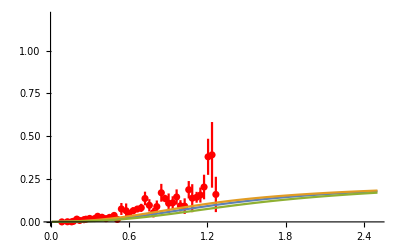

```mathematica
Show[AI[CurSet],AIDH[CurSet]]
```

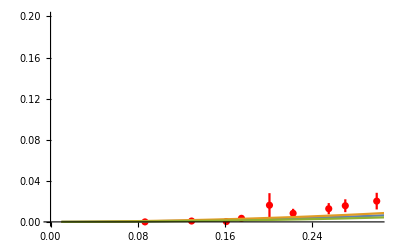

```mathematica
Show[AIClose[CurSet],AIDH[CurSet]]
```

```mathematica
"beta=6.900 T=164.2MeV Real Part";
```

```mathematica
CurSet=4;
```

```mathematica
Temp[CurSet]=0.1642;
```

```mathematica
CurBeta=6.90;
```

```mathematica
VaryAandCandS={  {AlphaInt[CurBeta],SigmaInt[CurBeta],ShiftCInt[CurBeta]},{AlphaInt[CurBeta],SigmaInt[CurBeta],ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta],SigmaInt[CurBeta],ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},
{AlphaInt[CurBeta],SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta],SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta],SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta],SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta],SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta],SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor}};
```

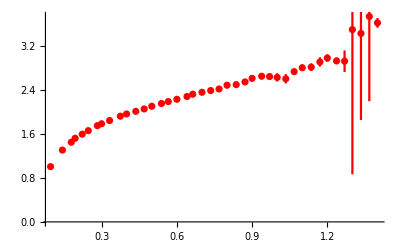

```mathematica
A[CurSet]=ErrorListPlot[PotReDataFull[CurSet],PlotStyle->{Red},PlotRange->All]
```

```mathematica
VaryFitLow={2,2,2,2,2,1,3,1,3};
VaryFitHigh={32,28,26,24,20,22,22,30,30}-2;
```

```mathematica
For[i=0,i<Length[VaryFitHigh],i++,
(*Here we vary the fitting range as specified by VaryFitLow and VaryFitHigh*)
For[j=0,j<27,j++,
(*Here we vary the for each fitting range the parameters determined at T=0*)

PotFit[CurSet][i*27+j]= NonlinearModelFit[PotReData[CurSet][[VaryFitLow[[i+1]];;VaryFitHigh[[i+1]] ]],{Re[DebyeHueckelReV[x,VaryAandCandS[[j+1]][[1]],VaryAandCandS[[j+1]][[2]],mD,VaryAandCandS[[j+1]][[3]]]]},{{mD,0.1}},x,Method->LevenbergMarquardt,MaxIterations->1000];mDTst[i*27+j]=mD/.PotFit[CurSet][i*27+j]["BestFitParameters"];
(*Print[mDTst[i*27+j]," "]*); ];]
```

```mathematica
mDFitted[CurSet]=Mean[Table[mDTst[k], {k,0,27*Length[VaryFitHigh]-1}]]
```

0.118382

```mathematica
mDFittedErr[CurSet]=StandardDeviation[Table[mDTst[k], {k,0,27*Length[VaryFitHigh]-1}]]
```

0.0353464

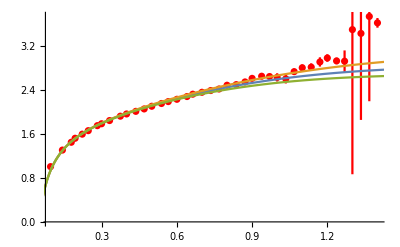

```mathematica
Show[A[CurSet],Plot[{Re[DebyeHueckelReV[r,AlphaInt[CurBeta],SigmaInt[CurBeta],mDFitted[CurSet],ShiftCInt[CurBeta]]],Re[DebyeHueckelReV[r,AlphaInt[CurBeta],SigmaInt[CurBeta],mDFitted[CurSet]-mDFittedErr[CurSet],ShiftCInt[CurBeta]]],Re[DebyeHueckelReV[r,AlphaInt[CurBeta],SigmaInt[CurBeta],mDFitted[CurSet]+mDFittedErr[CurSet],ShiftCInt[CurBeta]]]},{r,0.01,2},PlotRange->All]]
```

```mathematica
"Imaginary Part";
```

```mathematica
AI[CurSet]=ErrorListPlot[PotImDataFull[CurSet],PlotStyle->{Red},PlotRange->{{0,2.5},{0,1.2}}];
```

```mathematica
AIClose[CurSet]=ErrorListPlot[PotImDataFull[CurSet],PlotStyle->{Red},PlotRange->{{0,0.3},{0,0.2}}];
```

```mathematica
If[FileExistsQ[ToString@StringForm["./ResultsDynamical/ImVWronskian1_``.dat",CurSet]],ImVWronskian1=Import[ToString@StringForm["./ResultsDynamical/ImVWronskian1_``.dat",CurSet]],ImVWronskian1=FullImVWronskianAndMikko[mDFitted[CurSet],Temp[CurSet],AlphaInt[CurBeta],SigmaInt[CurBeta],10.];Export[ToString@StringForm["./ResultsDynamical/ImVWronskian1_``.dat",CurSet],ImVWronskian1,InterpolationOrder->2]];
```

```mathematica
InterpImVFull1[CurSet]=Interpolation[ImVWronskian1,InterpolationOrder->2];
```

```mathematica
If[FileExistsQ[ToString@StringForm["./ResultsDynamical/ImVWronskian2_``.dat",CurSet]],ImVWronskian2=Import[ToString@StringForm["./ResultsDynamical/ImVWronskian2_``.dat",CurSet]],ImVWronskian2=FullImVWronskianAndMikko[mDFitted[CurSet]+mDFittedErr[CurSet],Temp[CurSet],AlphaInt[CurBeta],SigmaInt[CurBeta],10.];Export[ToString@StringForm["./ResultsDynamical/ImVWronskian2_``.dat",CurSet],ImVWronskian2,InterpolationOrder->2]];
```

```mathematica
InterpImVFull2[CurSet]=Interpolation[ImVWronskian2,InterpolationOrder->2];
```

```mathematica
If[FileExistsQ[ToString@StringForm["./ResultsDynamical/ImVWronskian3_``.dat",CurSet]],ImVWronskian3=Import[ToString@StringForm["./ResultsDynamical/ImVWronskian3_``.dat",CurSet]],ImVWronskian3=FullImVWronskianAndMikko[If[mDFitted[CurSet]-mDFittedErr[CurSet]>0,mDFitted[CurSet]-mDFittedErr[CurSet],mDFitted[CurSet]*0.1],Temp[CurSet],AlphaInt[CurBeta],SigmaInt[CurBeta],10.];Export[ToString@StringForm["./ResultsDynamical/ImVWronskian3_``.dat",CurSet],ImVWronskian3,InterpolationOrder->2]];
```

```mathematica
InterpImVFull3[CurSet]=Interpolation[ImVWronskian3,InterpolationOrder->2];
```

```mathematica
"Plotting the fit for ImV";
```

```mathematica
AIDH[CurSet]=Plot[{InterpImVFull1[CurSet][r],InterpImVFull2[CurSet][r],InterpImVFull3[CurSet][r]},{r,0.01,2.5}];
```

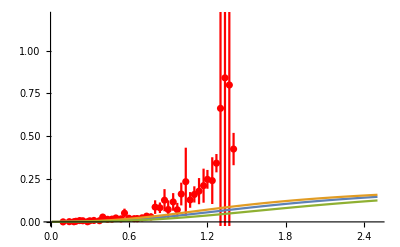

```mathematica
Show[AI[CurSet],AIDH[CurSet]]
```

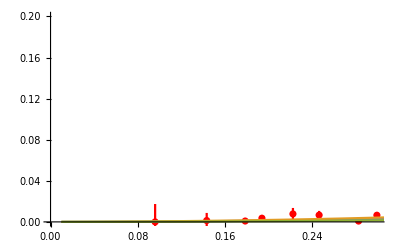

```mathematica
Show[AIClose[CurSet],AIDH[CurSet]]
```

```mathematica
"beta=6.800 T=147.8MeV Real Part";
```

```mathematica
CurSet=3;
```

```mathematica
Temp[CurSet]=0.1478;
```

```mathematica
CurBeta=6.80;
```

```mathematica
VaryAandCandS={  {AlphaInt[CurBeta],SigmaInt[CurBeta],ShiftCInt[CurBeta]},{AlphaInt[CurBeta],SigmaInt[CurBeta],ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta],SigmaInt[CurBeta],ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},
{AlphaInt[CurBeta],SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta],SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta],SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta],SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta],SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta],SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]+AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta],ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]+SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]+ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor},{AlphaInt[CurBeta]-AlphaInt[CurBeta]*AlphaRelErrInt[CurBeta]*VariationFactor,SigmaInt[CurBeta]-SigmaInt[CurBeta]*SigmaRelErrInt[CurBeta]*VariationFactor,ShiftCInt[CurBeta]-ShiftCInt[CurBeta]*ShiftCRelErrInt[CurBeta]*VariationFactor}};
```

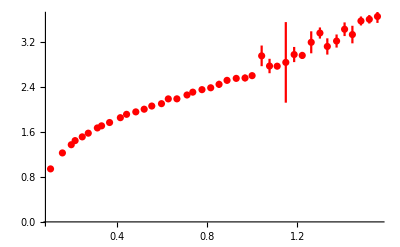

```mathematica
A[CurSet]=ErrorListPlot[PotReDataFull[CurSet],PlotStyle->{Red},PlotRange->All]
```

```mathematica
VaryFitLow={2,2,2,2,2,1,3,1,3};
VaryFitHigh={32,28,26,24,20,22,22,30,30}-2;
```

```mathematica
For[i=0,i<Length[VaryFitHigh],i++,
(*Here we vary the fitting range as specified by VaryFitLow and VaryFitHigh*)
For[j=0,j<27,j++,
(*Here we vary the for each fitting range the parameters determined at T=0*)

PotFit[CurSet][i*27+j]= NonlinearModelFit[PotReData[CurSet][[VaryFitLow[[i+1]];;VaryFitHigh[[i+1]] ]],{Re[DebyeHueckelReV[x,VaryAandCandS[[j+1]][[1]],VaryAandCandS[[j+1]][[2]],mD,VaryAandCandS[[j+1]][[3]]]]},{{mD,0.1}},x,Method->LevenbergMarquardt,MaxIterations->1000];mDTst[i*27+j]=mD/.PotFit[CurSet][i*27+j]["BestFitParameters"];
(*Print[mDTst[i*27+j]," "]*); ];]
```

```mathematica
mDFitted[CurSet]=Mean[Table[mDTst[k], {k,0,27*Length[VaryFitHigh]-1}]]
```

0.00661281

```mathematica
mDFittedErr[CurSet]=StandardDeviation[Table[mDTst[k], {k,0,27*Length[VaryFitHigh]-1}]]
```

0.0153154

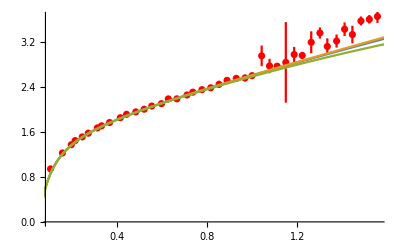

```mathematica
Show[A[CurSet],Plot[{Re[DebyeHueckelReV[r,AlphaInt[CurBeta],SigmaInt[CurBeta],mDFitted[CurSet],ShiftCInt[CurBeta]]],Re[DebyeHueckelReV[r,AlphaInt[CurBeta],SigmaInt[CurBeta],0.000001,ShiftCInt[CurBeta]]],Re[DebyeHueckelReV[r,AlphaInt[CurBeta],SigmaInt[CurBeta],mDFitted[CurSet]+mDFittedErr[CurSet],ShiftCInt[CurBeta]]]},{r,0.01,2},PlotRange->All]]
```

```mathematica
"Imaginary Part";
```

```mathematica
AI[CurSet]=ErrorListPlot[PotImDataFull[CurSet],PlotStyle->{Red},PlotRange->{{0,2.5},{0,1.2}}];
```

```mathematica
AIClose[CurSet]=ErrorListPlot[PotImDataFull[CurSet],PlotStyle->{Red},PlotRange->{{0,0.3},{0,0.2}}];
```

```mathematica
If[FileExistsQ[ToString@StringForm["./ResultsDynamical/ImVWronskian1_``.dat",CurSet]],ImVWronskian1=Import[ToString@StringForm["./ResultsDynamical/ImVWronskian1_``.dat",CurSet]],ImVWronskian1=FullImVWronskianAndMikko[mDFitted[CurSet],Temp[CurSet],AlphaInt[CurBeta],SigmaInt[CurBeta],10.];Export[ToString@StringForm["./ResultsDynamical/ImVWronskian1_``.dat",CurSet],ImVWronskian1,InterpolationOrder->2]];
```

```mathematica
InterpImVFull1[CurSet]=Interpolation[ImVWronskian1,InterpolationOrder->1];
```

```mathematica
If[FileExistsQ[ToString@StringForm["./ResultsDynamical/ImVWronskian2_``.dat",CurSet]],ImVWronskian2=Import[ToString@StringForm["./ResultsDynamical/ImVWronskian2_``.dat",CurSet]],ImVWronskian2=FullImVWronskianAndMikko[mDFitted[CurSet]+mDFittedErr[CurSet],Temp[CurSet],AlphaInt[CurBeta],SigmaInt[CurBeta],10.];Export[ToString@StringForm["./ResultsDynamical/ImVWronskian2_``.dat",CurSet],ImVWronskian2,InterpolationOrder->2]];
```

```mathematica
InterpImVFull2[CurSet]=Interpolation[ImVWronskian2,InterpolationOrder->2];
```

```mathematica
If[FileExistsQ[ToString@StringForm["./ResultsDynamical/ImVWronskian3_``.dat",CurSet]],ImVWronskian3=Import[ToString@StringForm["./ResultsDynamical/ImVWronskian3_``.dat",CurSet]],ImVWronskian3=FullImVWronskianAndMikko[If[mDFitted[CurSet]-mDFittedErr[CurSet]>0,mDFitted[CurSet]-mDFittedErr[CurSet],mDFitted[CurSet]*0.1],Temp[CurSet],AlphaInt[CurBeta],SigmaInt[CurBeta],10.];Export[ToString@StringForm["./ResultsDynamical/ImVWronskian3_``.dat",CurSet],ImVWronskian3,InterpolationOrder->2]];
```

```mathematica
InterpImVFull3[CurSet]=Interpolation[ImVWronskian3,InterpolationOrder->2];
```

```mathematica
"Plotting the fit for ImV";
```

```mathematica
AIDH[CurSet]=Plot[{InterpImVFull1[CurSet][r],InterpImVFull2[CurSet][r],InterpImVFull3[CurSet][r]},{r,0.01,2.5}];
```

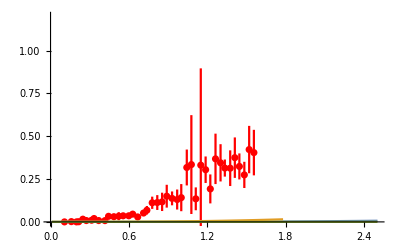

```mathematica
Show[AI[CurSet],AIDH[CurSet]]
```

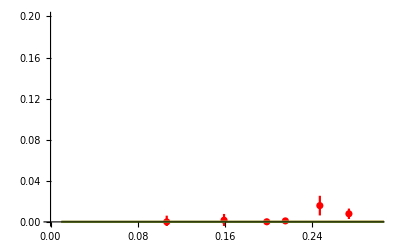

```mathematica
Show[AIClose[CurSet],AIDH[CurSet]]
```

```mathematica
"Now combine into single figure";
```

```mathematica
"Real Part";
```

```mathematica
BetA={6.9,7.48,6.8,6.9,7.0,7.125,7.25,7.3,7.48};
```

```mathematica
TempP={"T=41MeV","T=72MeV","T=148MeV","T=164MeV","T=182MeV","T=205MeV","T=232MeV","T=243MeV","T=286MeV"};
```

```mathematica
286/172.5
```

1.65797

```mathematica
TempP={"T=0.24T_C","T=0.42T_C","T=0.86T_C","T=0.95T_C","T=1.06T_C","T=1.19T_C","T=1.34T_C","T=1.41T_C","T=1.66T_C"};
```

```mathematica
TempP={"T≈0(β=6.9)","T≈0(β=7.48)","T=0.86T_C","T=0.95T_C","T=1.06T_C","T=1.19T_C","T=1.34T_C","T=1.41T_C","T=1.66T_C"};
```

```mathematica
For[l=1,l≤ 9,l++,PotReRescale[l]=Table[{PotReData[l][[k,1]],PotReData[l][[k,2]]-ShiftCInt[BetA[[l]]]-0.45*If[l==1,0,l]+2.1+3.7,PotReDataFull[l][[k,3]]},{k,1,If[l==8||l==9,Length[PotReData[l]]*0.7,Length[PotReData[l]]]}]]
```

```mathematica
For[l=1,l≤ 9,l++,PotImRescale[l]=Table[{PotImData[l][[k,1]]+0.1*l+3.5,PotReData[l][[k,2]],PotReDataFull[l][[k,3]]},{k,1,Length[PotReData[l]]}]]
```

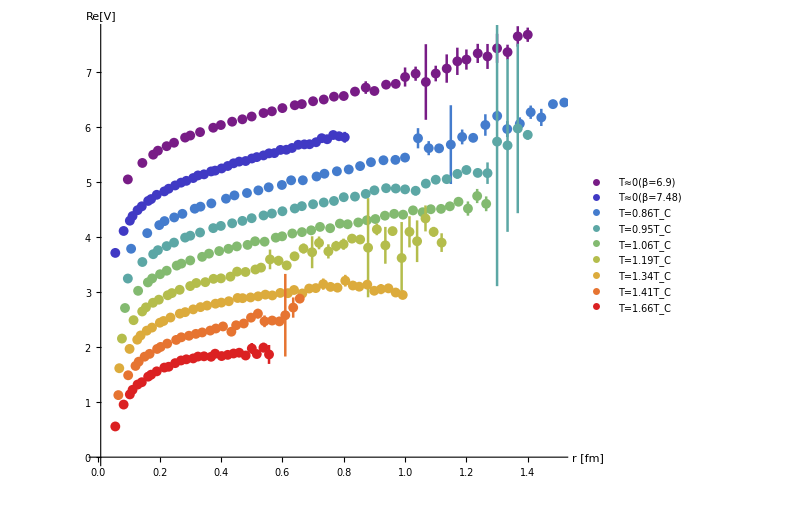

```mathematica
PReD=ErrorListPlot[Table[PotReRescale[l],{l,1,9}],PlotRange->{{0.00001,1.5},{0.,7.7}},PlotStyle->Thread@{AbsolutePointSize[7.1],AbsoluteThickness[1.8],ColorData["Rainbow"]/@Range[0,1,1/8]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},PlotLegends->Placed[PointLegend[TempP, LegendMarkerSize->8,LegendLayout->{"Row",3}],{0.66,0.12}],AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{600,600}]
```

```mathematica
MyMarkersFiniteT[s_]:={{Graphics@{RGBColor[0.471412, 0.108766, 0.527016],Disk[]},s},{Graphics@{RGBColor[0.31106, 0.11758, 0.664469],Rectangle[]},s},{Graphics@{RGBColor[0.250728, 0.225386, 0.769152],Polygon[CirclePoints[5]]},s},{Graphics@{RGBColor[0.24408, 0.361242, 0.816084],SSSTriangle[1,1,1]},s},{Graphics@{RGBColor[0.266122, 0.486664, 0.802529],Triangle[{{0,1},{1,1},{0.5,0}}]},s},{Graphics@{RGBColor[0.305919, 0.585575, 0.739666],Polygon[CirclePoints[6]]},s},{Graphics@{RGBColor[0.36048, 0.655759, 0.645692],Triangle[{{0,0.5},{1,1},{1,0}}]},s},{Graphics@{RGBColor[0.429842, 0.701849, 0.540321],Triangle[{{0,0},{0,1},{1,0.5}}]},s},{Graphics@{Antialiasing->False,Opacity[1],FaceForm[],EdgeForm[{RGBColor[0.513417, 0.72992, 0.440682],Thick}],Disk[]},s},{Graphics@{Antialiasing->False,Opacity[1],FaceForm[],EdgeForm[{RGBColor[0.607651, 0.743718, 0.358588],Thick}],Rectangle[]},s},{Graphics@{Antialiasing->False,Opacity[1],FaceForm[],EdgeForm[{RGBColor[0.705038, 0.742591, 0.299167],Thick}],Polygon[CirclePoints[5]]},s},{Graphics@{Antialiasing->False,Opacity[1],FaceForm[],EdgeForm[{RGBColor[0.794549, 0.721158, 0.260829],Thick}],SSSTriangle[1,1,1]},s},{Graphics@{Antialiasing->False,Opacity[1],FaceForm[],EdgeForm[{RGBColor[0.863512, 0.670771, 0.236564],Thick}],Triangle[{{0,1},{1,1},{0.5,0}}]},s},{Graphics@{Antialiasing->False,Opacity[1],FaceForm[],EdgeForm[{RGBColor[0.901014, 0.582826, 0.216542],Thick}],Polygon[CirclePoints[6]]},s},{Graphics@{Antialiasing->False,Opacity[1],FaceForm[],EdgeForm[{RGBColor[0.902853, 0.453964, 0.192014],Thick}],Triangle[{{0,0.5},{1,1},{1,0}}]},s},{Graphics@{Antialiasing->False,Opacity[1],FaceForm[],EdgeForm[{RGBColor[0.878107, 0.293208, 0.160481],Thick}],Triangle[{{0,0},{0,1},{1,0.5}}]},s},{Graphics@{Antialiasing->False,Opacity[1],FaceForm[],EdgeForm[{RGBColor[0.857359, 0.131106, 0.132128],Thick}],Polygon[CirclePoints[7]]},s}};
```

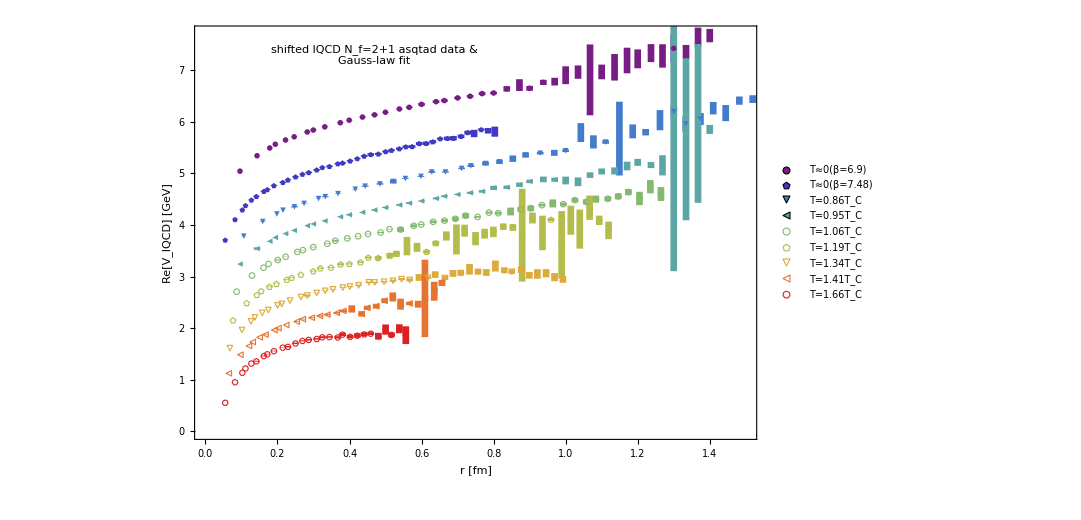

```mathematica
PReD=ErrorListPlot[Table[PotReRescale[l],{l,1,9}],PlotRange->{{0.00001,1.5},{0.,7.7}},PlotStyle->Thread@{AbsolutePointSize[7.1],AbsoluteThickness[4.8],ColorData["Rainbow"]/@Range[0,1,1/8]},Frame->{True,True,False,False},PlotMarkers->MyMarkersFiniteT[0.03][[;;;;2]],FrameStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},PlotLegends->Placed[PointLegend[TempP, LegendMarkerSize->15,LegendLayout->{"Row",3}],{0.66,0.12}],AspectRatio->0.65,FrameLabel->{"r [fm]","Re[V_lQCD] [GeV]"},ImageSize->{800,600},Epilog->Style[{Style[Text["shifted lQCD N_f=2+1 asqtad data &\nGauss-law fit",TextAlignment->Left,Scaled[{0.32,0.93}]],Gray]},25]]
```

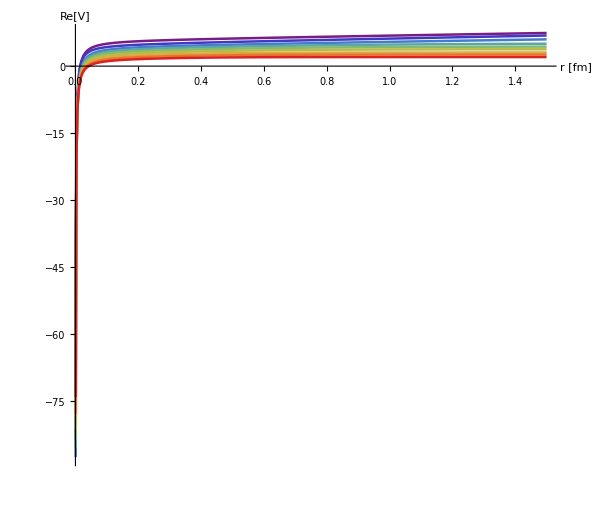

```mathematica
PReHF=Plot[{CornellReV[r,AlphaInt[6.9],SigmaInt[6.9],0]-0.45*0+2.1+3.7,CornellReV[r,AlphaInt[7.48],SigmaInt[7.48],0]-0.45*2+2.1+3.7,DebyeHueckelReV[r,AlphaInt[6.8],SigmaInt[6.8],mDFitted[3],0]-0.45*3+2.1+3.7,DebyeHueckelReV[r,AlphaInt[6.9],SigmaInt[6.9],mDFitted[4],0]-0.45*4+2.1+3.7,DebyeHueckelReV[r,AlphaInt[7.0],SigmaInt[7.0],mDFitted[5],0]-0.45*5+2.1+3.7,DebyeHueckelReV[r,AlphaInt[7.125],SigmaInt[7.125],mDFitted[6],0]-0.45*6+2.1+3.7,DebyeHueckelReV[r,AlphaInt[7.250],SigmaInt[7.250],mDFitted[7],0]-0.45*7+2.1+3.7,DebyeHueckelReV[r,AlphaInt[7.30],SigmaInt[7.3],mDFitted[8],0]-0.45*8+2.1+3.7,DebyeHueckelReV[r,AlphaInt[7.48],SigmaInt[7.48],mDFitted[9],0]-0.45*9+2.1+3.7},{r,0.001,1.5},PlotStyle->Thread@{AbsolutePointSize[7.1],AbsoluteThickness[1.8],ColorData["Rainbow"]/@Range[0,1,1/8]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{600,600},PlotRange->{{0,1.5},All}]
```

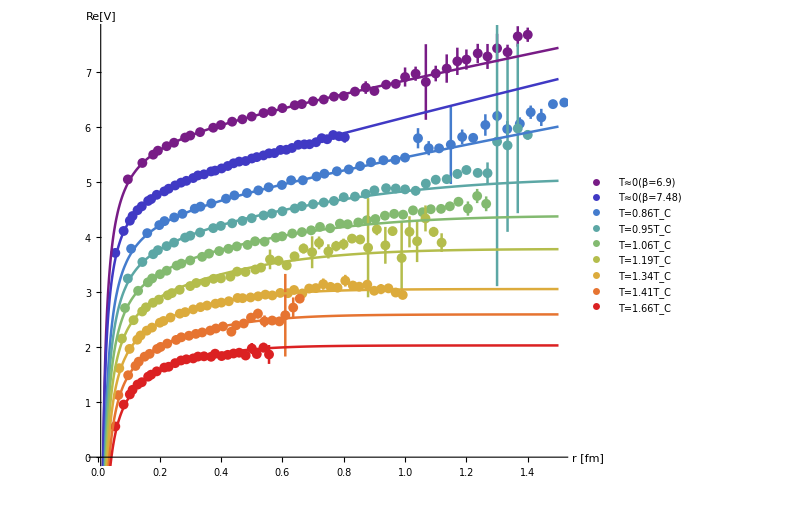

```mathematica
Show[PReD,PReHF]
```

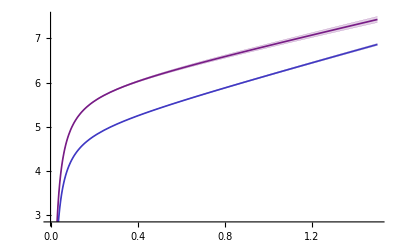

```mathematica
PReHF2=Plot[{

CornellReV[r,AlphaInt[6.9],SigmaInt[6.9]-SigmaInt[6.9]*SigmaRelErrInt[6.9],0]-0.45*0+2.1+3.7,
CornellReV[r,AlphaInt[6.9],SigmaInt[6.9],0]-0.45*0+2.1+3.7,
CornellReV[r,AlphaInt[6.9],SigmaInt[6.9]+SigmaInt[6.9]*SigmaRelErrInt[6.9],0]-0.45*0+2.1+3.7,

CornellReV[r,AlphaInt[7.48],SigmaInt[7.48]-SigmaInt[7.48]*SigmaRelErrInt[7.48],0]-0.45*2+2.1+3.7,
CornellReV[r,AlphaInt[7.48],SigmaInt[7.48],0]-0.45*2+2.1+3.7,
CornellReV[r,AlphaInt[7.48],SigmaInt[7.48]+SigmaInt[7.48]*SigmaRelErrInt[7.48],0]-0.45*2+2.1+3.7,
},{r,0,1.5}, Filling->{1-> {3}, 4->{6}, 7->{9}, 10->{12},13->{15}, 16->{18}, 19->{21}, 22->{24},25->{27}},

PlotStyle->{
{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][0/8]},{AbsolutePointSize[10],Thickness[0.003],ColorData["Rainbow"][0/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][0/8]},

{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][1/8]},{AbsolutePointSize[10],Thickness[0.003],ColorData["Rainbow"][1/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][1/8]},

{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][2/8]},{AbsolutePointSize[10],Thickness[0.003],ColorData["Rainbow"][2/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][2/8]},

{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][3/8]},{AbsolutePointSize[10],Thickness[0.003],ColorData["Rainbow"][3/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][3/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][4/8]},{AbsolutePointSize[10],Thickness[0.003],ColorData["Rainbow"][4/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][4/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][5/8]},{AbsolutePointSize[10],Thickness[0.003],ColorData["Rainbow"][5/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][5/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][6/8]},{AbsolutePointSize[10],Thickness[0.003],ColorData["Rainbow"][6/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][6/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][7/8]},{AbsolutePointSize[10],Thickness[0.003],ColorData["Rainbow"][7/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][7/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][8/8]},{AbsolutePointSize[10],Thickness[0.003],ColorData["Rainbow"][8/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][8/8]}}

]
```

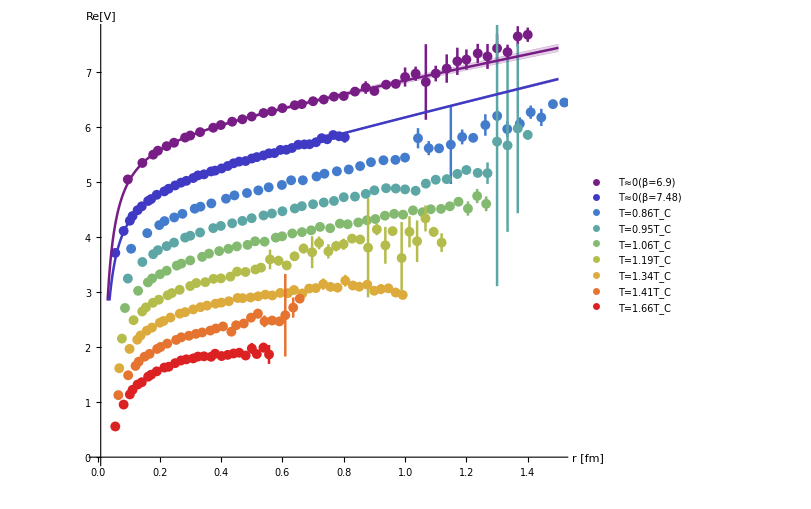

```mathematica
Show[PReD,PReHF2]
```

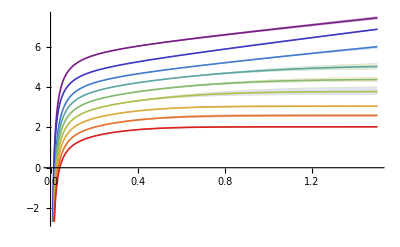

```mathematica
PReHF=Plot[{

CornellReV[r,AlphaInt[6.9],SigmaInt[6.9]-SigmaInt[6.9]*SigmaRelErrInt[6.9],0]-0.45*0+2.1+3.7,
CornellReV[r,AlphaInt[6.9],SigmaInt[6.9],0]-0.45*0+2.1+3.7,
CornellReV[r,AlphaInt[6.9],SigmaInt[6.9]+SigmaInt[6.9]*SigmaRelErrInt[6.9],0]-0.45*0+2.1+3.7,

CornellReV[r,AlphaInt[7.48],SigmaInt[7.48]-SigmaInt[7.48]*SigmaRelErrInt[7.48],0]-0.45*2+2.1+3.7,
CornellReV[r,AlphaInt[7.48],SigmaInt[7.48],0]-0.45*2+2.1+3.7,
CornellReV[r,AlphaInt[7.48],SigmaInt[7.48]+SigmaInt[7.48]*SigmaRelErrInt[7.48],0]-0.45*2+2.1+3.7,


DebyeHueckelReV[r,AlphaInt[6.8],SigmaInt[6.8],mDFitted[3]-mDFittedErr[3],0]-0.45*3+2.1+3.7,
DebyeHueckelReV[r,AlphaInt[6.8],SigmaInt[6.8],mDFitted[3],0]-0.45*3+2.1+3.7,
DebyeHueckelReV[r,AlphaInt[6.8],SigmaInt[6.8],mDFitted[3]+mDFittedErr[3],0]-0.45*3+2.1+3.7,

DebyeHueckelReV[r,AlphaInt[6.9],SigmaInt[6.9],mDFitted[4]-mDFittedErr[4],0]-0.45*4+2.1+3.7,
DebyeHueckelReV[r,AlphaInt[6.9],SigmaInt[6.9],mDFitted[4],0]-0.45*4+2.1+3.7,
DebyeHueckelReV[r,AlphaInt[6.9],SigmaInt[6.9],mDFitted[4]+mDFittedErr[4],0]-0.45*4+2.1+3.7,


DebyeHueckelReV[r,AlphaInt[7.0],SigmaInt[7.0],mDFitted[5]-mDFittedErr[5],0]-0.45*5+2.1+3.7,
DebyeHueckelReV[r,AlphaInt[7.0],SigmaInt[7.0],mDFitted[5],0]-0.45*5+2.1+3.7,
DebyeHueckelReV[r,AlphaInt[7.0],SigmaInt[7.0],mDFitted[5]+mDFittedErr[5],0]-0.45*5+2.1+3.7,

DebyeHueckelReV[r,AlphaInt[7.125],SigmaInt[7.125],mDFitted[6]-mDFittedErr[6],0]-0.45*6+2.1+3.7,
DebyeHueckelReV[r,AlphaInt[7.125],SigmaInt[7.125],mDFitted[6],0]-0.45*6+2.1+3.7,DebyeHueckelReV[r,AlphaInt[7.125],SigmaInt[7.125],mDFitted[6]+mDFittedErr[6],0]-0.45*6+2.1+3.7,

DebyeHueckelReV[r,AlphaInt[7.250],SigmaInt[7.250],mDFitted[7]-mDFittedErr[7],0]-0.45*7+2.1+3.7,
DebyeHueckelReV[r,AlphaInt[7.250],SigmaInt[7.250],mDFitted[7],0]-0.45*7+2.1+3.7,
DebyeHueckelReV[r,AlphaInt[7.250],SigmaInt[7.250],mDFitted[7]+mDFittedErr[7],0]-0.45*7+2.1+3.7,

DebyeHueckelReV[r,AlphaInt[7.30],SigmaInt[7.3],mDFitted[8]-mDFittedErr[8],0]-0.45*8+2.1+3.7,
DebyeHueckelReV[r,AlphaInt[7.30],SigmaInt[7.3],mDFitted[8],0]-0.45*8+2.1+3.7,
DebyeHueckelReV[r,AlphaInt[7.30],SigmaInt[7.3],mDFitted[8]+mDFittedErr[8],0]-0.45*8+2.1+3.7,

DebyeHueckelReV[r,AlphaInt[7.48],SigmaInt[7.48],mDFitted[9]-mDFittedErr[9],0]-0.45*9+2.1+3.7,
DebyeHueckelReV[r,AlphaInt[7.48],SigmaInt[7.48],mDFitted[9],0]-0.45*9+2.1+3.7,
DebyeHueckelReV[r,AlphaInt[7.48],SigmaInt[7.48],mDFitted[9]+mDFittedErr[9],0]-0.45*9+2.1+3.7
},{r,0,1.5}, Filling->{1-> {3}, 4->{6}, 7->{9}, 10->{12},13->{15}, 16->{18}, 19->{21}, 22->{24},25->{27}},

PlotStyle->{
{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][0/8]},{AbsolutePointSize[10],Thickness[0.003],ColorData["Rainbow"][0/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][0/8]},

{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][1/8]},{AbsolutePointSize[10],Thickness[0.003],ColorData["Rainbow"][1/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][1/8]},

{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][2/8]},{AbsolutePointSize[10],Thickness[0.003],ColorData["Rainbow"][2/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][2/8]},

{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][3/8]},{AbsolutePointSize[10],Thickness[0.003],ColorData["Rainbow"][3/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][3/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][4/8]},{AbsolutePointSize[10],Thickness[0.003],ColorData["Rainbow"][4/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][4/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][5/8]},{AbsolutePointSize[10],Thickness[0.003],ColorData["Rainbow"][5/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][5/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][6/8]},{AbsolutePointSize[10],Thickness[0.003],ColorData["Rainbow"][6/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][6/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][7/8]},{AbsolutePointSize[10],Thickness[0.003],ColorData["Rainbow"][7/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][7/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][8/8]},{AbsolutePointSize[10],Thickness[0.003],ColorData["Rainbow"][8/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][8/8]}}

]
```

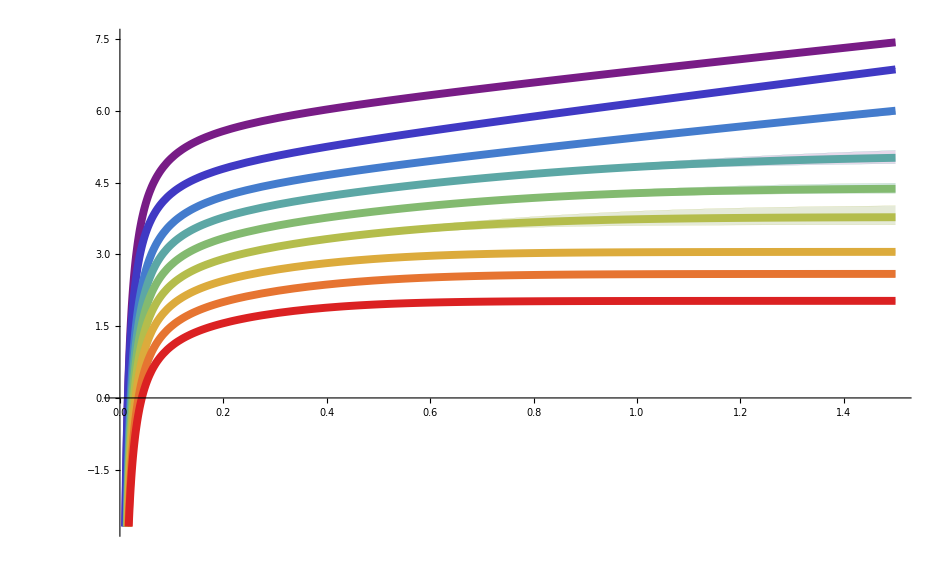

```mathematica
PReHF=Plot[{

CornellReV[r,AlphaInt[6.9],SigmaInt[6.9]-SigmaInt[6.9]*SigmaRelErrInt[6.9],0]-0.45*0+2.1+3.7,
CornellReV[r,AlphaInt[6.9],SigmaInt[6.9],0]-0.45*0+2.1+3.7,
CornellReV[r,AlphaInt[6.9],SigmaInt[6.9]+SigmaInt[6.9]*SigmaRelErrInt[6.9],0]-0.45*0+2.1+3.7,

CornellReV[r,AlphaInt[7.48],SigmaInt[7.48]-SigmaInt[7.48]*SigmaRelErrInt[7.48],0]-0.45*2+2.1+3.7,
CornellReV[r,AlphaInt[7.48],SigmaInt[7.48],0]-0.45*2+2.1+3.7,
CornellReV[r,AlphaInt[7.48],SigmaInt[7.48]+SigmaInt[7.48]*SigmaRelErrInt[7.48],0]-0.45*2+2.1+3.7,


DebyeHueckelReV[r,AlphaInt[6.8],SigmaInt[6.8],mDFitted[3]-mDFittedErr[3],0]-0.45*3+2.1+3.7,
DebyeHueckelReV[r,AlphaInt[6.8],SigmaInt[6.8],mDFitted[3],0]-0.45*3+2.1+3.7,
DebyeHueckelReV[r,AlphaInt[6.8],SigmaInt[6.8],mDFitted[3]+mDFittedErr[3],0]-0.45*3+2.1+3.7,

DebyeHueckelReV[r,AlphaInt[6.9],SigmaInt[6.9],mDFitted[4]-mDFittedErr[4],0]-0.45*4+2.1+3.7,
DebyeHueckelReV[r,AlphaInt[6.9],SigmaInt[6.9],mDFitted[4],0]-0.45*4+2.1+3.7,
DebyeHueckelReV[r,AlphaInt[6.9],SigmaInt[6.9],mDFitted[4]+mDFittedErr[4],0]-0.45*4+2.1+3.7,


DebyeHueckelReV[r,AlphaInt[7.0],SigmaInt[7.0],mDFitted[5]-mDFittedErr[5],0]-0.45*5+2.1+3.7,
DebyeHueckelReV[r,AlphaInt[7.0],SigmaInt[7.0],mDFitted[5],0]-0.45*5+2.1+3.7,
DebyeHueckelReV[r,AlphaInt[7.0],SigmaInt[7.0],mDFitted[5]+mDFittedErr[5],0]-0.45*5+2.1+3.7,

DebyeHueckelReV[r,AlphaInt[7.125],SigmaInt[7.125],mDFitted[6]-mDFittedErr[6],0]-0.45*6+2.1+3.7,
DebyeHueckelReV[r,AlphaInt[7.125],SigmaInt[7.125],mDFitted[6],0]-0.45*6+2.1+3.7,DebyeHueckelReV[r,AlphaInt[7.125],SigmaInt[7.125],mDFitted[6]+mDFittedErr[6],0]-0.45*6+2.1+3.7,

DebyeHueckelReV[r,AlphaInt[7.250],SigmaInt[7.250],mDFitted[7]-mDFittedErr[7],0]-0.45*7+2.1+3.7,
DebyeHueckelReV[r,AlphaInt[7.250],SigmaInt[7.250],mDFitted[7],0]-0.45*7+2.1+3.7,
DebyeHueckelReV[r,AlphaInt[7.250],SigmaInt[7.250],mDFitted[7]+mDFittedErr[7],0]-0.45*7+2.1+3.7,

DebyeHueckelReV[r,AlphaInt[7.30],SigmaInt[7.3],mDFitted[8]-mDFittedErr[8],0]-0.45*8+2.1+3.7,
DebyeHueckelReV[r,AlphaInt[7.30],SigmaInt[7.3],mDFitted[8],0]-0.45*8+2.1+3.7,
DebyeHueckelReV[r,AlphaInt[7.30],SigmaInt[7.3],mDFitted[8]+mDFittedErr[8],0]-0.45*8+2.1+3.7,

DebyeHueckelReV[r,AlphaInt[7.48],SigmaInt[7.48],mDFitted[9]-mDFittedErr[9],0]-0.45*9+2.1+3.7,
DebyeHueckelReV[r,AlphaInt[7.48],SigmaInt[7.48],mDFitted[9],0]-0.45*9+2.1+3.7,
DebyeHueckelReV[r,AlphaInt[7.48],SigmaInt[7.48],mDFitted[9]+mDFittedErr[9],0]-0.45*9+2.1+3.7
},{r,0,1.5}, Filling->{{1-> {3}}, 4->{6}, 7->{9}, 10->{12},13->{15},{ 16->{18}}, 19->{21}, 22->{24},25->{27}},
FillingStyle->{1->ColorData["Rainbow"][0/8],2->ColorData["Rainbow"][1/8],3->ColorData["Rainbow"][2/8],4->ColorData["Rainbow"][3/8],5->ColorData["Rainbow"][4/8],6->ColorData["Rainbow"][5/8],7->ColorData["Rainbow"][6/8],8->ColorData["Rainbow"][7/8],9->ColorData["Rainbow"][8/8]},
PlotStyle->{
{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][0/8]},{AbsolutePointSize[10],Thickness[0.006],ColorData["Rainbow"][0/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][0/8]},

{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][1/8]},{AbsolutePointSize[10],Thickness[0.006],ColorData["Rainbow"][1/8]},{AbsolutePointSize[10],Thickness[0.0006],ColorData["Rainbow"][1/8]},

{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][2/8]},{AbsolutePointSize[10],Thickness[0.006],ColorData["Rainbow"][2/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][2/8]},

{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][3/8]},{AbsolutePointSize[10],Thickness[0.006],ColorData["Rainbow"][3/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][3/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][4/8]},{AbsolutePointSize[10],Thickness[0.006],ColorData["Rainbow"][4/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][4/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][5/8]},{AbsolutePointSize[10],Thickness[0.006],ColorData["Rainbow"][5/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][5/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][6/8]},{AbsolutePointSize[10],Thickness[0.006],ColorData["Rainbow"][6/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][6/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][7/8]},{AbsolutePointSize[10],Thickness[0.006],ColorData["Rainbow"][7/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][7/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][8/8]},{AbsolutePointSize[10],Thickness[0.006],ColorData["Rainbow"][8/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][8/8]}}

]
```

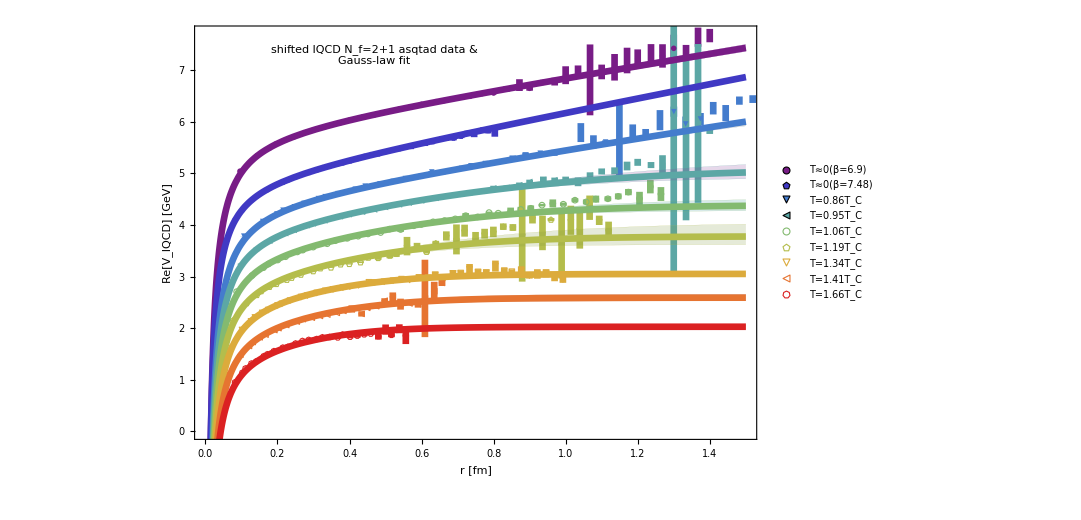

```mathematica
X=Show[PReD,PReHF]
```

```mathematica
Export["QQbarReVFullQCDRaw.pdf", X]
```

QQbarReVFullQCDRaw.pdf

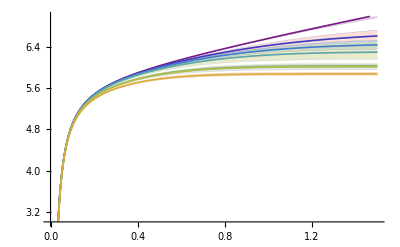

```mathematica
PReHF3=Plot[{

DebyeHueckelReV[r,0.5,0.415^2,mDFitted[3]-mDFittedErr[3],0]-0.0*3+2.1+3.7,
DebyeHueckelReV[r,0.5,0.415^2,mDFitted[3],0]-0.0*3+2.1+3.7,
DebyeHueckelReV[r,0.5,0.415^2,mDFitted[3]+mDFittedErr[3],0]-0.0*3+2.1+3.7,

DebyeHueckelReV[r,0.5,0.415^2,mDFitted[4]-mDFittedErr[4],0]-0.0*4+2.1+3.7,
DebyeHueckelReV[r,0.5,0.415^2,mDFitted[4],0]-0.0*4+2.1+3.7,
DebyeHueckelReV[r,0.5,0.415^2,mDFitted[4]+mDFittedErr[4],0]-0.0*4+2.1+3.7,


DebyeHueckelReV[r,0.5,0.415^2,mDFitted[5]-mDFittedErr[5],0]-0.0*5+2.1+3.7,
DebyeHueckelReV[r,0.5,0.415^2,mDFitted[5],0]-0.0*5+2.1+3.7,
DebyeHueckelReV[r,0.5,0.415^2,mDFitted[5]+mDFittedErr[5],0]-0.0*5+2.1+3.7,

DebyeHueckelReV[r,0.5,0.415^2,mDFitted[6]-mDFittedErr[6],0]-0.0*6+2.1+3.7,
DebyeHueckelReV[r,0.5,0.415^2,mDFitted[6],0]-0.0*6+2.1+3.7,DebyeHueckelReV[r,0.5,0.415^2,mDFitted[6]+mDFittedErr[6],0]-0.0*6+2.1+3.7,

DebyeHueckelReV[r,0.5,0.415^2,mDFitted[7]-mDFittedErr[7],0]-0.0*7+2.1+3.7,
DebyeHueckelReV[r,0.5,0.415^2,mDFitted[7],0]-0.0*7+2.1+3.7,
DebyeHueckelReV[r,0.5,0.415^2,mDFitted[7]+mDFittedErr[7],0]-0.0*7+2.1+3.7,

DebyeHueckelReV[r,0.5,0.415^2,mDFitted[8]-mDFittedErr[8],0]-0.0*8+2.1+3.7,
DebyeHueckelReV[r,0.5,0.415^2,mDFitted[8],0]-0.0*8+2.1+3.7,
DebyeHueckelReV[r,0.5,0.415^2,mDFitted[8]+mDFittedErr[8],0]-0.0*8+2.1+3.7,

DebyeHueckelReV[r,0.5,0.415^2,mDFitted[9]-mDFittedErr[9],0]-0.0*9+2.1+3.7,
DebyeHueckelReV[r,0.5,0.415^2,mDFitted[9],0]-0.0*9+2.1+3.7,
DebyeHueckelReV[r,0.5,0.415^2,mDFitted[9]+mDFittedErr[9],0]-0.0*9+2.1+3.7
},{r,0,1.5},PlotRange->{3,7}, Filling->{1-> {3}, 4->{6}, 7->{9}, 10->{12},13->{15}, 16->{18}, 19->{21}, 22->{24},25->{27}},

PlotStyle->{
{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][0/8]},{AbsolutePointSize[10],Thickness[0.003],ColorData["Rainbow"][0/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][0/8]},

{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][1/8]},{AbsolutePointSize[10],Thickness[0.003],ColorData["Rainbow"][1/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][1/8]},

{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][2/8]},{AbsolutePointSize[10],Thickness[0.003],ColorData["Rainbow"][2/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][2/8]},

{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][3/8]},{AbsolutePointSize[10],Thickness[0.003],ColorData["Rainbow"][3/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][3/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][4/8]},{AbsolutePointSize[10],Thickness[0.003],ColorData["Rainbow"][4/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][4/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][5/8]},{AbsolutePointSize[10],Thickness[0.003],ColorData["Rainbow"][5/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][5/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][6/8]},{AbsolutePointSize[10],Thickness[0.003],ColorData["Rainbow"][6/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][6/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][7/8]},{AbsolutePointSize[10],Thickness[0.003],ColorData["Rainbow"][7/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][7/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][8/8]},{AbsolutePointSize[10],Thickness[0.003],ColorData["Rainbow"][8/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][8/8]}}

]
```

```mathematica
Clear[a,s,m,c]
```

```mathematica
Series[DebyeHueckelReV[0.197x,a,s,m,c],{x,0,2}]
```

-(1. a)/x+c+(-0.5 a m^2+1. s) x+0.166667 a m^3 x^2+O[x]^3

```mathematica
"Imaginary Part";
```

```mathematica
Shift=0.8
```

0.8

```mathematica
For[l=1,l≤ 9,l++,PotImRescale[l]=Table[{PotImData[l][[k,1]]-Shift*l+9*Shift,PotImData[l][[k,2]],PotImDataFull[l][[k,3]]},{k,1,Length[PotReData[l]]}]]
```

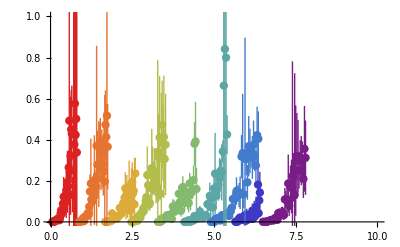

```mathematica
PImD=ErrorListPlot[Table[PotImRescale[l],{l,1,9}],PlotRange->{{0,10},{0,1}},PlotStyle->Thread@{AbsolutePointSize[6],AbsoluteThickness[1.],ColorData["Rainbow"]/@Range[0,1,1/8]}]
```

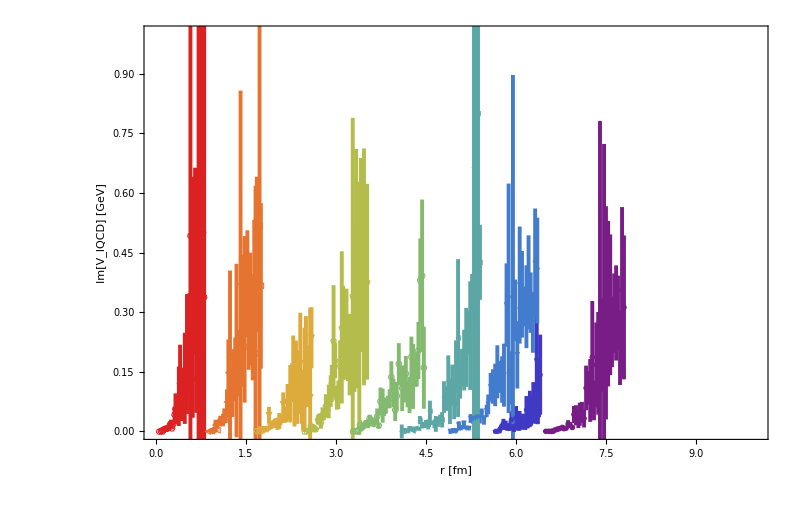

```mathematica
PImD=ErrorListPlot[Table[PotImRescale[l],{l,1,9}],PlotRange->{{0,10},{0,1}},Frame->{True,True,False,False},PlotStyle->Thread@{AbsolutePointSize[7.1],AbsoluteThickness[2.8],ColorData["Rainbow"]/@Range[0,1,1/8]},PlotMarkers->MyMarkersFiniteT[0.03][[;;;;2]],FrameStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.65,FrameLabel->{"r [fm]","-Im[V_lQCD] [GeV]"},ImageSize->{800,600}]
```

```mathematica
PReD=ErrorListPlot[Table[PotReRescale[l],{l,1,9}],PlotRange->{{0.00001,1.5},{0.,7.7}},PlotStyle->Thread@{AbsolutePointSize[7.1],AbsoluteThickness[4.8],ColorData["Rainbow"]/@Range[0,1,1/8]},Frame->{True,True,False,False},PlotMarkers->MyMarkersFiniteT[0.03][[;;;;2]],FrameStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},PlotLegends->Placed[PointLegend[TempP, LegendMarkerSize->15,LegendLayout->{"Row",3}],{0.66,0.12}],AspectRatio->0.65,FrameLabel->{"r [fm]","Re[V] [GeV]"},ImageSize->{800,600}]
```

```mathematica
Temps={41.05,71.54,147.8,164.2,181.8,205.4,231.7,242.5,286.1}/1000
```

{0.04105,0.07154,0.1478,0.1642,0.1818,0.2054,0.2317,0.2425,0.2861}

```mathematica
DHImVFitFuncs2={
Table[{k-0.45*0+4.05,0},{k,0.01,9.9,9.9/100}],
Table[{k-0.45*0+4.05,0},{k,0.01,9.9,9.9/100}],
Table[{k-0.45*0+4.05,0},{k,0.01,9.9,9.9/100}],

Table[{k-0.45*1+4.05,0},{k,0.01,9.9,9.9/100}],
Table[{k-0.45*1+4.05,0},{k,0.01,9.9,9.9/100}],
Table[{k-0.45*1+4.05,0},{k,0.01,9.9,9.9/100}],

Table[{k-0.45*3+4.05,InterpImVFull3[3][k]},{k,0.01,9.9,9.9/100}],Table[{k-0.45*3+4.05,InterpImVFull1[3][k]},{k,0.01,9.9,9.9/100}],Table[{k-0.45*3+4.05,InterpImVFull2[3][k]},{k,0.01,9.9,9.9/100}],

Table[{k-0.45*4+4.05,InterpImVFull3[4][k]},{k,0.01,9.9,9.9/100}],Table[{k-0.45*4+4.05,InterpImVFull1[4][k]},{k,0.01,9.9,9.9/100}],Table[{k-0.45*4+4.05,InterpImVFull2[4][k]},{k,0.01,9.9,9.9/100}],

Table[{k-0.45*5+4.05,InterpImVFull3[5][k]},{k,0.01,9.9,9.9/100}],Table[{k-0.45*5+4.05,InterpImVFull1[5][k]},{k,0.01,9.9,9.9/100}],Table[{k-0.45*5+4.05,InterpImVFull2[5][k]},{k,0.01,9.9,9.9/100}],

Table[{k-0.45*6+4.05,InterpImVFull3[6][k]},{k,0.01,9.9,9.9/100}],Table[{k-0.45*6+4.05,InterpImVFull1[6][k]},{k,0.01,9.9,9.9/100}],Table[{k-0.45*6+4.05,InterpImVFull2[6][k]},{k,0.01,9.9,9.9/100}],

Table[{k-0.45*7+4.05,InterpImVFull3[7][k]},{k,0.01,9.9,9.9/100}],Table[{k-0.45*7+4.05,InterpImVFull1[7][k]},{k,0.01,9.9,9.9/100}],Table[{k-0.45*7+4.05,InterpImVFull2[7][k]},{k,0.01,9.9,9.9/100}],

Table[{k-0.45*8+4.05,InterpImVFull3[8][k]},{k,0.01,9.9,9.9/100}],Table[{k-0.45*8+4.05,InterpImVFull1[8][k]},{k,0.01,9.9,9.9/100}],Table[{k-0.45*8+4.05,InterpImVFull2[8][k]},{k,0.01,9.9,9.9/100}],

Table[{k-0.45*9+4.05,InterpImVFull3[9][k]},{k,0.01,9.9,9.9/100}],Table[{k-0.45*9+4.05,InterpImVFull1[9][k]},{k,0.01,9.9,9.9/100}],Table[{k-0.45*9+4.05,InterpImVFull2[9][k]},{k,0.01,9.9,9.9/100}]
};
```

```mathematica
DHImVFitFuncs3={
Table[{k-Shift*3+9*Shift,InterpImVFull3[3][k]},{k,0.01,9.9,9.9/100}],Table[{k-Shift*3+9*Shift,InterpImVFull1[3][k]},{k,0.01,9.9,9.9/100}],Table[{k-Shift*3+9*Shift,InterpImVFull2[3][k]},{k,0.01,9.9,9.9/100}],

Table[{k-Shift*4+9*Shift,InterpImVFull3[4][k]},{k,0.01,9.9,9.9/100}],Table[{k-Shift*4+9*Shift,InterpImVFull1[4][k]},{k,0.01,9.9,9.9/100}],Table[{k-Shift*4+9*Shift,InterpImVFull2[4][k]},{k,0.01,9.9,9.9/100}],

Table[{k-Shift*5+9*Shift,InterpImVFull3[5][k]},{k,0.01,9.9,9.9/100}],Table[{k-Shift*5+9*Shift,InterpImVFull1[5][k]},{k,0.01,9.9,9.9/100}],Table[{k-Shift*5+9*Shift,InterpImVFull2[5][k]},{k,0.01,9.9,9.9/100}],

Table[{k-Shift*6+9*Shift,InterpImVFull3[6][k]},{k,0.01,9.9,9.9/100}],Table[{k-Shift*6+9*Shift,InterpImVFull1[6][k]},{k,0.01,9.9,9.9/100}],Table[{k-Shift*6+9*Shift,InterpImVFull2[6][k]},{k,0.01,9.9,9.9/100}],

Table[{k-Shift*7+9*Shift,InterpImVFull3[7][k]},{k,0.01,9.9,9.9/100}],Table[{k-Shift*7+9*Shift,InterpImVFull1[7][k]},{k,0.01,9.9,9.9/100}],Table[{k-Shift*7+9*Shift,InterpImVFull2[7][k]},{k,0.01,9.9,9.9/100}],

Table[{k-Shift*8+9*Shift,InterpImVFull3[8][k]},{k,0.01,9.9,9.9/100}],Table[{k-Shift*8+9*Shift,InterpImVFull1[8][k]},{k,0.01,9.9,9.9/100}],Table[{k-Shift*8+9*Shift,InterpImVFull2[8][k]},{k,0.01,9.9,9.9/100}],

Table[{k-Shift*9+9*Shift,InterpImVFull3[9][k]},{k,0.01,9.9,9.9/100}],Table[{k-Shift*9+9*Shift,InterpImVFull1[9][k]},{k,0.01,9.9,9.9/100}],Table[{k-Shift*9+9*Shift,InterpImVFull2[9][k]},{k,0.01,9.9,9.9/100}]
};
```

```mathematica
TempP={None,"T=41MeV",None,None,"T=72MeV",None,None,"T=148MeV",None,None,"T=164MeV",None,None,"T=182MeV",None,None,"T=205MeV",None,None,"T=232MeV",None,None,"T=243MeV",None,None,"T=286MeV",None};
```

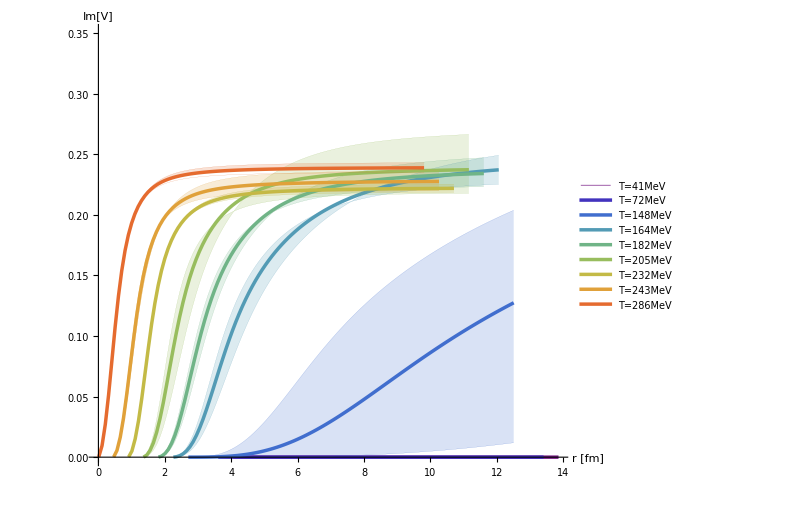

```mathematica
PImHF1=ListPlot[DHImVFitFuncs2,Joined->True, Filling->{1-> {2}, 4->{6}, 7->{9}, 10->{12},13->{15}, 16->{18}, 19->{21}, 22->{24},25->{26}},PlotStyle->{
{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][0/9]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][0/9]},
{AbsolutePointSize[10],AbsoluteThickness[2.5],ColorData["Rainbow"][0/9]},
{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][1/9]},{AbsolutePointSize[10],AbsoluteThickness[2.5],ColorData["Rainbow"][1/9]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][1/9]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][2/9]},{AbsolutePointSize[10],AbsoluteThickness[2.5],ColorData["Rainbow"][2/9]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][2/9]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][3/9]},{AbsolutePointSize[10],AbsoluteThickness[2.5],ColorData["Rainbow"][3/9]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][3/9]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][4/9]},{AbsolutePointSize[10],AbsoluteThickness[2.5],ColorData["Rainbow"][4/9]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][4/9]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][5/9]},{AbsolutePointSize[10],AbsoluteThickness[2.5],ColorData["Rainbow"][5/9]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][5/9]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][6/9]},{AbsolutePointSize[10],AbsoluteThickness[2.5],ColorData["Rainbow"][6/9]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][6/9]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][7/9]},{AbsolutePointSize[10],AbsoluteThickness[2.5],ColorData["Rainbow"][7/9]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][7/9]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][8/9]},{AbsolutePointSize[10],AbsoluteThickness[2.5],ColorData["Rainbow"][8/9]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][8/9]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][9/9]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][9/9]},
{AbsolutePointSize[10],AbsoluteThickness[2.5],ColorData["Rainbow"][9/9]}},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},PlotLegends->Placed[PointLegend[TempP, LegendMarkerSize->20,LegendLayout->{"Row",3}],{0.45,0.85}],AspectRatio->0.85,PlotRange->{0,0.35},AxesLabel->{"r [fm]","Im[V]"},ImageSize->{600,600}]
```

```mathematica
TempP2={None,"T=148MeV",None,None,"T=164MeV",None,None,"T=182MeV",None,None,"T=205MeV",None,None,"T=232MeV",None,None,"T=243MeV",None,None,"T=286MeV"};
```

```mathematica
TempP2={None,"T=0.86T_C",None,None,"T=0.95T_C",None,None,"T=1.06T_C",None,None,"T=1.19T_C",None,None,"T=1.34T_C",None,None,"T=1.41T_C",None,None,"T=1.66T_C"};
```

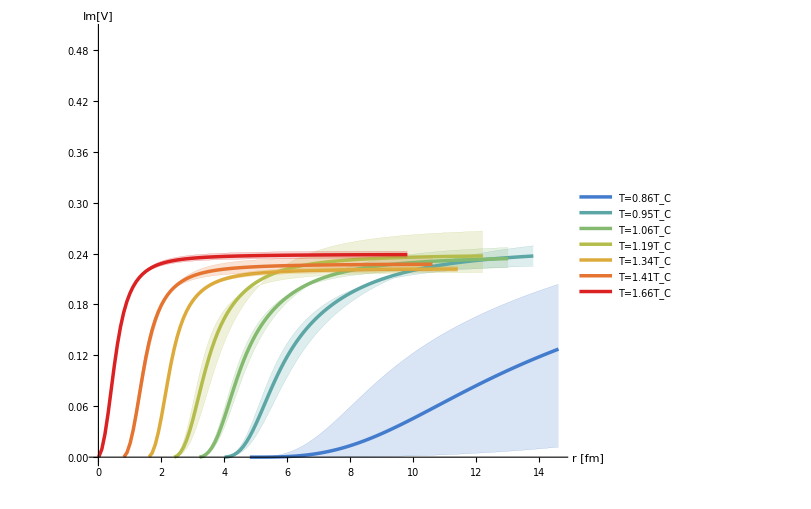

```mathematica
PImHF1=ListPlot[DHImVFitFuncs3,Joined->True,PlotStyle->{
{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][2/8]},{AbsolutePointSize[10],AbsoluteThickness[2.5],ColorData["Rainbow"][2/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][2/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][3/8]},{AbsolutePointSize[10],AbsoluteThickness[2.5],ColorData["Rainbow"][3/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][3/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][4/8]},{AbsolutePointSize[10],AbsoluteThickness[2.5],ColorData["Rainbow"][4/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][4/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][5/8]},{AbsolutePointSize[10],AbsoluteThickness[2.5],ColorData["Rainbow"][5/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][5/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][6/8]},{AbsolutePointSize[10],AbsoluteThickness[2.5],ColorData["Rainbow"][6/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][6/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][7/8]},{AbsolutePointSize[10],AbsoluteThickness[2.5],ColorData["Rainbow"][7/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][7/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][8/8]},{AbsolutePointSize[10],AbsoluteThickness[2.5],ColorData["Rainbow"][8/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][8/8]}},Filling->{1-> {3}, 4->{6}, 7->{9}, 10->{12},13->{15}, 16->{18}, 19->{21}, 22->{23},25->{27}},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->16},PlotLegends->Placed[PointLegend[TempP2, LegendMarkerSize->20, LegendFunction->(Framed[#,RoundingRadius->2,FrameStyle->White,Background->White]&),LegendLayout->{"Row",3}],{0.47,0.875}],AspectRatio->0.85,PlotRange->{0,0.5},AxesLabel->{"r [fm]","Im[V]"},ImageSize->{600,600}]
```

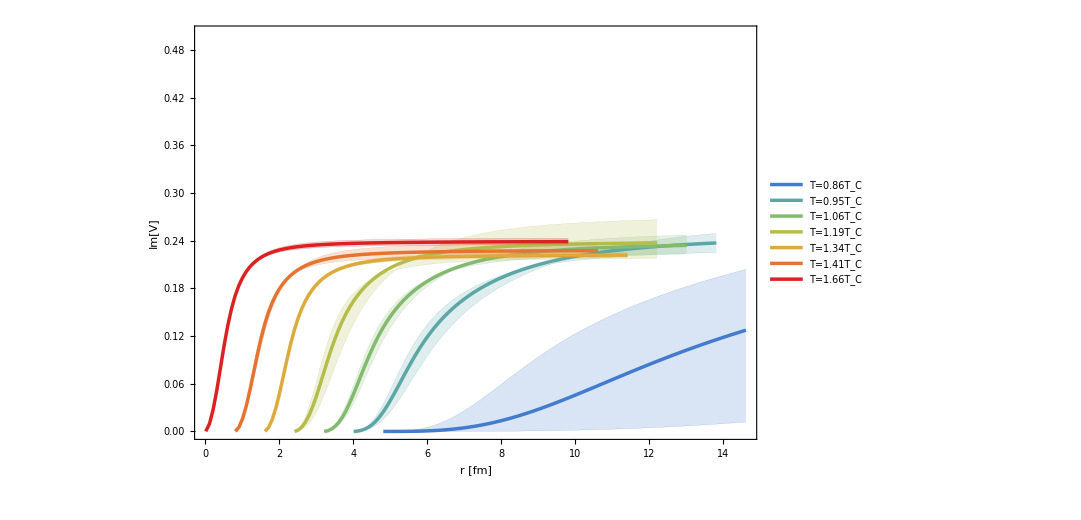

```mathematica
PImHF1=ListPlot[DHImVFitFuncs3,Joined->True,PlotStyle->{
{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][2/8]},{AbsolutePointSize[10],AbsoluteThickness[2.5],ColorData["Rainbow"][2/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][2/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][3/8]},{AbsolutePointSize[10],AbsoluteThickness[2.5],ColorData["Rainbow"][3/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][3/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][4/8]},{AbsolutePointSize[10],AbsoluteThickness[2.5],ColorData["Rainbow"][4/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][4/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][5/8]},{AbsolutePointSize[10],AbsoluteThickness[2.5],ColorData["Rainbow"][5/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][5/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][6/8]},{AbsolutePointSize[10],AbsoluteThickness[2.5],ColorData["Rainbow"][6/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][6/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][7/8]},{AbsolutePointSize[10],AbsoluteThickness[2.5],ColorData["Rainbow"][7/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][7/8]},{AbsolutePointSize[10],Thickness[0.00001],ColorData["Rainbow"][8/8]},{AbsolutePointSize[10],AbsoluteThickness[2.5],ColorData["Rainbow"][8/8]},{AbsolutePointSize[10],Thickness[0.0001],ColorData["Rainbow"][8/8]}},Filling->{1-> {3}, 4->{6}, 7->{9}, 10->{12},13->{15}, 16->{18}, 19->{21}, 22->{23},25->{27}},Frame->{True,True,False,False},FrameStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->16},PlotLegends->Placed[PointLegend[TempP2, LegendMarkerSize->20, LegendFunction->(Framed[#,RoundingRadius->2,FrameStyle->White,Background->White]&),LegendLayout->{"Row",3}],{0.73,0.89}],AspectRatio->0.65,PlotRange->{0,0.5},FrameLabel->{"r [fm]","Im[V]"},ImageSize->{800,600}]
```

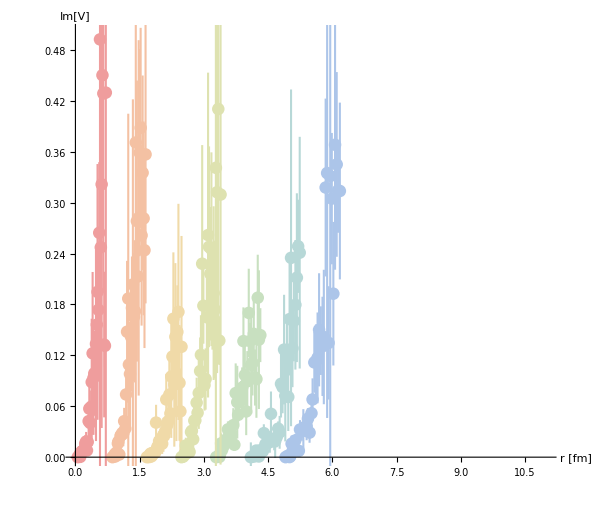

```mathematica
PImD=ErrorListPlot[Table[PotImRescale[l][[1;;Floor[Length[PotImRescale[l]]*0.9]]],{l,3,9}],PlotRange->{{0,11},{0,0.5}},PlotStyle->Thread@{AbsolutePointSize[9],AbsoluteThickness[1.5],Lighter[Lighter[ColorData["Rainbow"]/@Range[2/8,1,1/8]]]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->16},AspectRatio->0.85,PlotRange->{0,0.35},AxesLabel->{"r [fm]","Im[V]"},ImageSize->{600,600}]
```

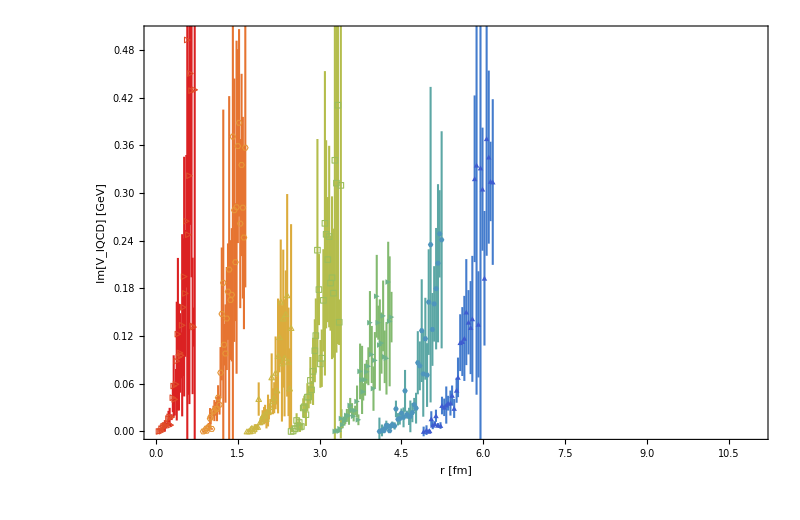

```mathematica
PImD=ErrorListPlot[Table[PotImRescale[l][[1;;Floor[Length[PotImRescale[l]]*0.9]]],{l,3,9}],Frame->{True,True,False,False}, PlotRange->{{0,11},{0,0.5}},Frame->{True,True,False,False},PlotMarkers->MyMarkersFiniteT[0.03][[4;;;;2]],PlotStyle->Thread@{AbsolutePointSize[9],AbsoluteThickness[1.5],ColorData["Rainbow"]/@Range[2/8,1,1/8]},FrameStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->16},AspectRatio->0.65,PlotRange->{0,0.35},FrameLabel->{"r [fm]","Im[V_lQCD] [GeV]"},ImageSize->{800,600}]
```

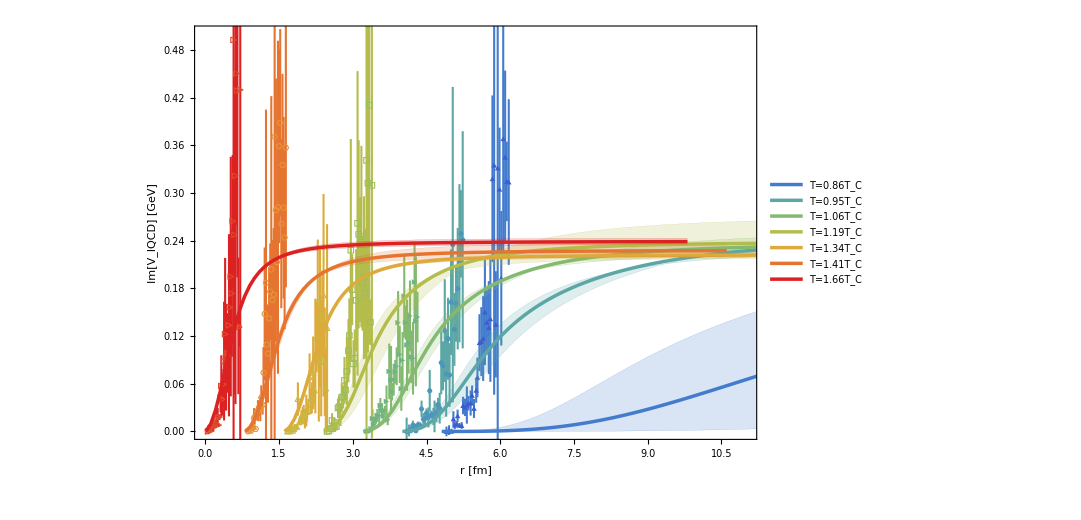

```mathematica
X=Show[PImD,PImHF1]
```

```mathematica
Export["QQbarImVFullQCDRaw.pdf", X]
```

QQbarImVFullQCDRaw.pdf

```mathematica
"Now compare Debye Masses to HTL";
```

```mathematica
"Need to do the continuum corection of the Debye mass";
```

```mathematica
"Setup renormalization group equations for the running coupling";
```

```mathematica
(* form hep-ph 9703284, vermaseren, larin, Ritbergen *)
ΛQCD=0.2145; 
(* so that for nF=5 we get alpha_s(mz=91.188)=0.1185 (PDG value) 
note that pdg also quotes λqcd=0.214 for nf=5 everything seems consistent*)

Clear[Nf,m4,M,μ];
Mref=1;
(*QCD*)
Nc=3.;CA=Nc;
CF=(Nc^2-1)/(2 Nc);
(*coeft of the renormalization group equations*)
β0[Nf_]=(-11Nc+2Nf)/12;
β1[Nf_]=(-68Nc^2+20Nc Nf+12CF Nf)/(3*32);
β2[Nf_]=-(2857-5033/9 Nf+325/27 Nf^2)/128; (*for Nc=3 only*)
β3[Nf_]=-1/256((149753/6+3564 Zeta[3])-(1078361/162+6508/27 Zeta[3])Nf+(50065/162+6472/81 Zeta[3])Nf^2+1093/729 Nf^3);(*for Nc=3 only*)

γ0[Nf_]=1/4(3 CF);
γ1[Nf_]=1/16(202/3-20/9Nf);(*for Nc=3 only*)
γ2[Nf_]=1/64(1249+(-2216/27-160/3 Zeta[3])Nf-140/81 Nf^2);(*for Nc=3 only*)
γ3[Nf_]=1/256(4603055/162+135680/27 Zeta[3]-8800Zeta[5]+(-91723/27-34192/9 Zeta[3]+880 Zeta[4]+18400/9 Zeta[5])Nf+(5242/243+800/9 Zeta[3]-160/3Zeta[4])Nf^2+(-332/243+64/27 Zeta[3])Nf^3);

b0[Nf_]=-8  β0[Nf]/2/ (4π)^2;
b1[Nf_]=-32 β1[Nf]/2 /(4π)^4;

(* Initial conditions of the RG equations, μ in units of Λ_MSbar *)

(*gf[μ_]=1/√(2 b0 Log[μ]+b1 Log[2 Log[μ]]/b0);*)
gf[t_]=1/√(b0[Nf] t+b1[Nf] Log[t]/b0[Nf]);
asf[t_,Nf_]=-1/(β0[Nf] t)-(β1[Nf] Log[t])/(β0[Nf]^3 t^2)-(β1[Nf]^2(Log[t]^2-Log[t]-1)+β2[Nf] β0[Nf])/(β0[Nf]^5t^3)+1/(β0[Nf]^7t^4)( β1[Nf]^3(-Log[t]^3+5/2Log[t]^2+2Log[t]-1/2)-3 β1[Nf] β2[Nf] β0[Nf] Log[t]+β3[Nf] β0[Nf]^2/2);
μ0=2;
t0=Log[μ0^2]; tf=10000*t0;
μref=2;
tref=Log[μref^2/ΛQCD^2];
mref=Log[Mref];
(*solution of the RG equation to 3 loop*)
Print["g"]
mcharm=1.275;(*m(m) in msbar*)
mbottom=4.18;
nf[t_]=If[t<Log[mcharm^2/ΛQCD^2],3,If[t<Log[mbottom^2/ΛQCD^2],4,5]];
sg4=NDSolve[{ D[as[t],t]==+β0[nf[t]] as[t]^2+β1[nf[t]] as[t]^3+ β2[nf[t]] as[t]^4+ β3[nf[t]] as[t]^5,as[tf]==asf[tf,nf[tf]]},as,{t,t0,tf},AccuracyGoal->14,WorkingPrecision->32,MaxSteps->10000000];

Print["ln(m)"];
a4t[t_]= Part[Evaluate[as[t]/.sg4],1];

(*
a3t[t_]= Part[Evaluate[as[t]/.sg3],1];
sg3=NDSolve[{ D[as[t],t]==+β0[nf[t]] as[t]^2+β1[nf[t]] as[t]^3+ β2[nf[t]] as[t]^4,as[tf]==asf[tf]},as,{t,t0,tf},AccuracyGoal->20];
sm4=NDSolve[{D[lnmq[t],t]==-γ0[nf[t]] a4t[t]-γ1[nf[t]] a4t[t]^2-γ2[nf[t]] a4t[t]^3-γ3[nf[t]] a4t[t]^4,lnmq[tref]==mref},lnmq,{t,t0,tf},AccuracyGoal->20,WorkingPrecision->32,MaxSteps->1000000];
Print["ln(m)2"];
sm3=NDSolve[{D[lnmq[t],t]==-γ0[nf[t]] a3t[t]-γ1[nf[t]] a3t[t]^2-γ2[nf[t]] a3t[t]^3,lnmq[tref]==mref},lnmq,{t,t0,tf},AccuracyGoal->20];
m4[μ_]=Part[Evaluate[Exp[lnmq[Log[μ^2/ΛQCD^2]]]/.sm4],1];
m3[μ_]=Part[Evaluate[Exp[lnmq[Log[μ^2/ΛQCD^2]]]/.sm3],1];
(*coupling/mass from 3 loop RG equation, mu in units of GeV *)
m4m=μ/.FindRoot[m4[μ]==μ,{μ,3}]
a3[μ_]=π Part[Evaluate[as[Log[μ^2/ΛQCD^2]]/.sg3],1]; (* α_s/π *)
g3[μ_]=2 π √Part[Evaluate[as[Log[μ^2/ΛQCD^2]]/.sg3],1]; (* g_s *)*)
a4[μ_]=π Part[Evaluate[as[Log[μ^2/ΛQCD^2]]/.sg4],1]; (* α_s/π *)
g4[μ_]=2 π √Part[Evaluate[as[Log[μ^2/ΛQCD^2]]/.sg4],1]; (* g_s *)
a4[91.188]
Plot[g4[t],{t,1,100},PlotRange->All]
```

```mathematica
"Continuum string tension";
```

```mathematica
sPhys=0.415^2
```

```mathematica
"Use RG coupling to determine HTL Debye Masses";
```

```mathematica
Betas={6.8,6.9,7.0,7.125,7.25,7.3,7.480};
```

```mathematica
TTRaw={41.05,71.54,147.8,164.2,181.8,205.4,231.7,242.5,286.1}/1000
```

```mathematica
TT={41.05,71.54,147.8,164.2,181.8,205.4,231.7,242.5,286.1}(155/172.5)/1000
```

```mathematica
BetaVsT=Table[{Betas[[k]],TT[[k+2]]},{k,1,7}]
```

```mathematica
TVsBeta=Table[{TT[[k+2]],Betas[[k]]},{k,1,7}]
```

```mathematica
ListPlot[TVsBeta]
```

```mathematica
TFromBeta=Interpolation[BetaVsT];
```

```mathematica
BetaFromT=Interpolation[TVsBeta];
```

```mathematica
Temps=TT;
```

```mathematica
TempsTc=Table[Round[Temps[[n]]/0.155,0.01],{n,1,9}]
```

```mathematica
nF=3;μbar=2π;
mD[μ_,T_,c_,d_]:=Re[Sqrt[Nc/3+nF/6]g4[μ T]T+1/(4 π)Nc g4[μ T]^2 T Log[Sqrt[Nc/3+nF/6]/g4[μ T]]+c g4[μ T]^2 T+   d g4[μ T]^3 T ];
(*mD[μ_,T_,c_,d_]=Sqrt[Nc/3+nF/6]g[μ T]T+c g[μ T]^2 T +  d g[μ T]^3 T;*)
```

```mathematica
MuValTab=Table[{k,mDFitted[k],mDFittedErr[k]},{k,1,9}]
```

```mathematica
MuValTab={{1,0.,0.},{2,0.,0.},{3,0.006612806775178447,0.015315378411673065},{4,0.11838248779708219,0.03534637332185927},{5,0.18708032935992522,0.04026938438624869},{6,0.262888303621937,0.09993022530371719},{7,0.47970799755273597,0.026445011490851933},{8,0.4971567208131331,0.0653965965966671},{9,0.6554067025702345,0.03934111497357126}}
```

```mathematica
MuValTabCont=Table[{k,mDFitted[k]*Sqrt[sPhys]/Sqrt[SigmaInt[BetA[[k]]]],mDFittedErr[k]},{k,1,9}]
```

```mathematica
MuValTabCont={{1,0.,0.},{2,0.,0.},{3,0.005923994957158252,0.015315378411673065},{4,0.10427715923648455,0.03534637332185927},{5,0.16212198926847815,0.04026938438624869},{6,0.2233770754126916,0.09993022530371719},{7,0.39996455529619385,0.026445011490851933},{8,0.41146603780340424,0.0653965965966671},{9,0.5286812826217437,0.03934111497357126}}
```

```mathematica
/(Sqrt[SigmaInt[BetaFromT[T]]]
```

```mathematica
Tfit=NonlinearModelFit[Table[{TT[[n]],MuValTabCont[[n]][[2]]},{n,3,9}],{mD[μbar,T,c,d]},{{d,-0.1},{c,0.2}},T,Method->LevenbergMarquardt,MaxIterations->1000]
Tfitmin=NonlinearModelFit[Table[{TT[[n]],MuValTabCont[[n]][[2]]-MuValTab[[n]][[3]]},{n,3,9}],{mD[μbar,T,c,d]},{{d,-0.1},{c,0.2}},T,Method->LevenbergMarquardt,MaxIterations->1000]
Tfitmax=NonlinearModelFit[Table[{TT[[n]],MuValTabCont[[n]][[2]]+MuValTab[[n]][[3]]},{n,3,9}],{mD[μbar,T,c,d]},{{d,-0.1},{c,0.2}},T,Method->LevenbergMarquardt,MaxIterations->1000]
parammin=Tfitmin["BestFitParameters"]
param=Tfit["BestFitParameters"]

parammax=Tfitmax["BestFitParameters"]
```

```mathematica
Show[ErrorListPlot[Table[{Temps[[n]],MuValTab[[n]][[2]]/(Sqrt[SigmaInt[BetA[[n]]]]),MuValTab[[n]][[3]]/(Sqrt[SigmaInt[BetA[[n]]]])},{n,3,9}],AxesLabel->{"T [GeV]","m_D/√σ"},PlotRange->{{0.14,0.345},{0.,1.45}},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->17},PlotStyle->{ {Thickness[0.008],PointSize->0.025}},ImageSize->{600,600},AspectRatio->0.85,AxesLabel->{"T [GeV]","m_D/√σ"}],Plot[{mD[μbar, T,c/.param,d/.param]/(Sqrt[SigmaInt[BetaFromT[T]]]),mD[μbar, T,c/.parammin,d/.parammin]/(Sqrt[SigmaInt[BetaFromT[T]]]),mD[μbar, T,c/.parammax,d/.parammax]/(Sqrt[SigmaInt[BetaFromT[T]]])},{T,Temps[[3]],0.35},PlotStyle->{{Red,Thick},None,None},Filling->{2->{3}},FillingStyle->{Hue[0,1,1,0.3]},PlotRange->{0.,3}, AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->17},AspectRatio->0.85]]
Show[ErrorListPlot[Table[{TempsTc[[n]],MuValTab[[n]][[2]]/(Sqrt[SigmaInt[BetA[[n]]]]),MuValTab[[n]][[3]]/(Sqrt[SigmaInt[BetA[[n]]]])},{n,3,9}],AxesLabel->{"T/T_C","m_D/√σ"},PlotRange->{{0.75,1.8},{0.,1.45}},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->17},PlotStyle->{ {Thickness[0.008],PointSize->0.025}},ImageSize->{600,600},AspectRatio->0.85,AxesLabel->{"T/T_C","m_D/√σ"}],Plot[{mD[μbar, T*0.1725,c/.param,d/.param]/(Sqrt[SigmaInt[BetaFromT[T*0.1725]]]),mD[μbar, T*0.1725,c/.parammin,d/.parammin]/(Sqrt[SigmaInt[BetaFromT[T*0.1725]]]),mD[μbar, T*0.1725,c/.parammax,d/.parammax]/(Sqrt[SigmaInt[BetaFromT[T*0.1725]]])},{T,TempsTc[[3]],0.35/0.1725},PlotStyle->{{Red,Thickness[0.008]},None,None},Filling->{2->{3}},FillingStyle->{Hue[0,1,1,0.3]},PlotRange->{0.,3}, AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->17},AspectRatio->0.85]]
Show[ErrorListPlot[Table[{TempsTc[[n]],MuValTab[[n]][[2]]/(Sqrt[SigmaInt[BetA[[n]]]]),MuValTab[[n]][[3]]/(Sqrt[SigmaInt[BetA[[n]]]])},{n,3,9}],AxesLabel->{"T/T_C","m_D/√σ"},PlotRange->{{0.75,1.8},{0.,1.45}},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->17},PlotStyle->{ {Thickness[0.008],PointSize->0.025}},ImageSize->{600,600},AspectRatio->0.85,AxesLabel->{"T/T_C","m_D/√σ"}]]
Show[ErrorListPlot[Table[{TempsTc[[n]],MuValTab[[n]][[2]]/(Sqrt[SigmaInt[BetA[[n]]]]),MuValTab[[n]][[3]]/(Sqrt[SigmaInt[BetA[[n]]]])},{n,3,9}],AxesLabel->{"T/T_C","m_D/√σ"},PlotRange->{{0.75,1.8},{0.,1.45}},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->17},PlotStyle->{ {Thickness[0.008],PointSize->0.025}},ImageSize->{600,600},AspectRatio->0.6,AxesLabel->{"T/T_C","m_D/√σ"}]]


Show[ErrorListPlot[Table[{Temps[[n]],MuValTab[[n]][[2]]/Temps[[n]],MuValTab[[n]][[3]]/Temps[[n]]},{n,1,9}],AxesLabel->{"T [GeV]","m_D/T"},PlotRange->{{0.02,0.345},{0.,2.95}},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->17},PlotStyle->{ {Thickness[0.008],PointSize->0.025}},ImageSize->{600,600},AspectRatio->0.85,AxesLabel->{"T [GeV]","m_D/T"}],Plot[{mD[μbar, T,c/.param,d/.param]/T,mD[μbar, T,c/.parammin,d/.parammin]/T,mD[μbar, T,c/.parammax,d/.parammax]/T},{T,Temps[[3]],0.35},PlotStyle->{{Red,Thick},None,None},Filling->{2->{3}},FillingStyle->{Hue[0,1,1,0.3]},PlotRange->{0.,3}, AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->17},AspectRatio->0.85]]

Show[ErrorListPlot[Table[{Temps[[n]],MuValTab[[n]][[2]]/Temps[[n]],MuValTab[[n]][[3]]/Temps[[n]]},{n,1,9}],AxesLabel->{"T [GeV]","m_D/T"},PlotRange->{{0.02,0.345},{0.,2.95}},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->17},PlotStyle->{ {Thickness[0.008],PointSize->0.025}},ImageSize->{600,600},AspectRatio->0.85,AxesLabel->{"T [GeV]","m_D/T"}]]

Show[ErrorListPlot[Table[{TempsTc[[n]],MuValTab[[n]][[2]]/Temps[[n]],MuValTab[[n]][[3]]/Temps[[n]]},{n,1,9}],AxesLabel->{"T/T_C","m_D/T"},PlotRange->{{0.02/0.1725,0.345/0.1725},{0.,2.95}},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->17},PlotStyle->{ {Thickness[0.008],PointSize->0.025}},ImageSize->{600,600},AspectRatio->0.85,AxesLabel->{"T/T_C","m_D/T"}],Plot[{mD[μbar, T*0.1725,c/.param,d/.param]/(T*0.1725),mD[μbar, T*0.1725,c/.parammin,d/.parammin]/(T*0.1725),mD[μbar, T*0.1725,c/.parammax,d/.parammax]/(T*0.1725)},{T,TempsTc[[3]],0.35/0.1725},PlotStyle->{{Red,Thickness[0.008]},None,None},Filling->{2->{3}},FillingStyle->{Hue[0,1,1,0.3]},PlotRange->{0.,3}, AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->17},AspectRatio->0.85]]

Show[ErrorListPlot[Table[{TempsTc[[n]],MuValTab[[n]][[2]]/Temps[[n]],MuValTab[[n]][[3]]/Temps[[n]]},{n,1,9}],AxesLabel->{"T/T_C","m_D/T"},PlotRange->{{0.75,1.8},{0.,2.95}},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->17},PlotStyle->{ {Thickness[0.008],PointSize->0.025}},ImageSize->{600,600},AspectRatio->0.85,AxesLabel->{"T/T_C","m_D/T"}]]

Show[ErrorListPlot[Table[{TempsTc[[n]],MuValTab[[n]][[2]]/Temps[[n]],MuValTab[[n]][[3]]/Temps[[n]]},{n,1,9}],AxesLabel->{"T/T_C","m_D/T"},PlotRange->{{0.75,1.8},{0.,2.95}},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->17},PlotStyle->{ {Thickness[0.008],PointSize->0.025}},ImageSize->{600,600},AspectRatio->0.6,AxesLabel->{"T/T_C","m_D/T"}]]

ErrorListPlot[Table[{Temps[[n]],MuValTab[[n]][[2]]/Sqrt[SigmaInt[BetA[[n]]]],Sqrt[ (MuValTab[[n]][[3]]/Sqrt[SigmaInt[BetA[[n]]]])^2+ (0.5*MuValTab[[n]][[2]]*Sqrt[SigmaInt[BetA[[n]]]]*Sqrt[SigmaRelErrInt[BetA[[n]]]]/Sqrt[SigmaInt[BetA[[n]]]]^3)^2]},{n,3,9}],AxesLabel->{"T [GeV]","m_D/√σ"},PlotRange->{0,1.5},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->17},PlotStyle->{ {Thickness[0.008],PointSize->0.025}},ImageSize->{600,600},AspectRatio->0.85]
```

```mathematica
mDDivSqrtSigma=Table[{T,mD[μbar, T,c/.param,d/.param]/(Sqrt[SigmaInt[BetaFromT[T]]])},{T,0.155,0.400,(0.4-0.145)/150}];
```

```mathematica
ListPlot[mDDivSqrtSigma]
```

```mathematica
Export["./mDTableDynamicalNew.dat",mDDivSqrtSigma]
```

```mathematica
mD[μbar, 0.152,c/.param,d/.param]
```

```mathematica
mD[μbar, 0.174,c/.param,d/.param]
```

```mathematica
mD[μbar, 0.200,c/.param,d/.param]
```

```mathematica
mD[μbar, 0.271,c/.param,d/.param]
```

```mathematica
mD[μbar, 0.1725,c/.param,d/.param]
```

```mathematica
BetaFromT[0.1725]
```

```mathematica
Sqrt[SigmaInt[BetaFromT[0.1725]]]
```

```mathematica
SigmaCont=0.415^2
```

```mathematica
(mD[μbar, 0.1725,c/.param,d/.param]*Sqrt[SigmaCont]/Sqrt[SigmaInt[BetaFromT[0.1725]]])
```

```mathematica
(mD[μbar, 0.1725,c/.param,d/.param]*Sqrt[SigmaCont]/Sqrt[SigmaInt[BetaFromT[0.1725]]])/0.155
```